## Import Utils

```mathematica
Get["D:\\Documents\\workspace\\课题\\workspace\\Local\\Public\\mathematica\\PN_inverse\\InversePNUtils.nb"];
```

```mathematica
(*NotebookEvaluate["D:\\Documents\\workspace\\课题\\PN_inverse\\InversePNUtils.nb"]*)
```

```mathematica
NotebookEvaluate["D:\\Documents\\workspace\\课题\\workspace\\Local\\Public\\mathematica\\PN_inverse\\InversePNUtils.nb"]
```

输入Mc范围：{8,15}

输入q范围：{1,20}

m1范围：{9.18959,91.4002}

m2范围：{2.43734,17.2305}

输入Mc范围：{6,13}

输入q范围：{1,7}

m1范围：{6.89219,42.9142}

m2范围：{2.8295,14.9331}

全局极小值结果：{0.,{m1→3.,m2→3.,spin1z→0.99,spin2z→0.99}}

全局极大值结果：{0.,{m1→3.,m2→3.,spin1z→0.99,spin2z→0.99}}

全局极小值结果：{2.81559×10^-11,{m1→46.8969,m2→60.4341,spin1z→0.435746,spin2z→-0.638885}}

全局极大值结果：{8.65708,{m1→100.,m2→3.,spin1z→0.99,spin2z→0.99}}

全局极小值结果：{8.47209×10^-10,{m1→60.1419,m2→76.87,spin1z→0.320417,spin2z→-0.443897}}

全局极大值结果：{1.94773,{m1→100.,m2→3.,spin1z→0.99,spin2z→0.99}}

## 设置non-GR参数字符flag Gw@150914!

```mathematica
eventID="GW170823";

deviationType="cpsi";
deviationOrders=List[0,2,3,4,"5l",6,"6l"];
deviationNames=List["cpsi0","cpsi2","cpsi3","cpsi4","cpsi5l","cpsi6","cpsi6l"];
psiNames=List["psi0","psi2","psi3","psi4","psi5l","psi6","psi6l"];

deviationType="cpsi";
deviationOrders=List[0,2,4,"5l",6,"6l",7];
deviationNames=List["cpsi0","cpsi2","cpsi4","cpsi5l","cpsi6","cpsi6l","cpsi7"];
psiNames=List["psi0","psi2","psi4","psi5l","psi6","psi6l","psi7"];

deviationType="cpsi";
deviationOrders=List[0,2,3,4,"5l",6,"6l",7];
deviationNames=List["cpsi0","cpsi2","cpsi3","cpsi4","cpsi5l","cpsi6","cpsi6l","cpsi7"];
psiNames=List["psi0","psi2","psi3","psi4","psi5l","psi6","psi6l","psi7"];
```

```mathematica
csvPath="D:\\Documents\\workspace\\课题\\workspace\\Local\\Parameterized_PN_Tests\\csv"<>"\\"<>eventID;
csvNames=eventID<>"_"<>#<>".csv"& /@ deviationNames;

csvFilePaths=csvPath<>"\\"<>#& /@ csvNames;
```

### from CSV

```mathematica
samples=<||>;
Do[
CSVSamples=Import["D:\\Documents\\workspace\\课题\\workspace\\Local\\Parameterized_PN_Tests\\csv\\"<>eventID<>"\\"<>eventID<>"_"<>n<>".csv"];
samples[n]=<||>;
samples[n]["mass1"]=CSVSamples[[All,1]][[2;;]];
samples[n]["mass2"]=CSVSamples[[All,2]][[2;;]];
samples[n]["spin1z"]=CSVSamples[[All,3]][[2;;]];
samples[n]["spin2z"]=CSVSamples[[All,4]][[2;;]];
samples[n]["eta"]=CSVSamples[[All,5]][[2;;]];
samples[n]["Mchirp"]=CSVSamples[[All,6]][[2;;]];
samples[n][n]=CSVSamples[[All,7]][[2;;]];
samples[n]["chis"]=χs[samples["spin1z"],samples["spin2z"]];
samples[n]["chia"]=χa[samples["spin1z"],samples["spin2z"]];,
{n,deviationNames}
]
```

### Calculate GR Coefficients

```mathematica
Do[
samples[deviationNames[[n]]][psiNames[[n]]]=MapThread[
Psi[deviationOrders[[n]],η[#1,#2],M[#1,#2],#3,#4]&,
{samples[deviationNames[[n]]]["mass1"],samples[deviationNames[[n]]]["mass2"],samples[deviationNames[[n]]]["spin1z"],samples[deviationNames[[n]]]["spin2z"]}
];,
{n,Range[Length[deviationOrders]]}
]
```

### Calculate BCIs

```mathematica
BCI=<||>;
Do[
BCI[deviationNames[[n]]]=<||>;
BCI[deviationNames[[n]]]["mass1"]=PlotParameterWithBCI[samples[deviationNames[[n]]]["mass1"],Subscript["m","1"]][[1]];
BCI[deviationNames[[n]]]["mass2"]=PlotParameterWithBCI[samples[deviationNames[[n]]]["mass2"],Subscript["m","2"]][[1]];
BCI[deviationNames[[n]]]["spin1z"]=PlotParameterWithBCI[samples[deviationNames[[n]]]["spin1z"],"spin1z"][[1]];
BCI[deviationNames[[n]]]["spin2z"]=PlotParameterWithBCI[samples[deviationNames[[n]]]["spin2z"],"spin2z"][[1]];
BCI[deviationNames[[n]]][deviationNames[[n]]]=PlotParameterWithBCI[samples[deviationNames[[n]]][deviationNames[[n]]],deviationNames[[n]]][[1]];
BCI[deviationNames[[n]]][psiNames[[n]]]=PlotParameterWithBCI[samples[deviationNames[[n]]][psiNames[[n]]],psiNames[[n]]][[1]];,
{n,Range[Length[deviationOrders]]}
]
```

```mathematica
widths={};
Do[
AppendTo[widths,(BCI[deviationNames[[n]]][deviationNames[[n]]][[3]]-BCI[deviationNames[[n]]][deviationNames[[n]]][[1]])/(BCI[deviationNames[[n]]][psiNames[[n]]][[3]]-BCI[deviationNames[[n]]][psiNames[[n]]][[1]])],
{n,Range[Length[deviationOrders]]}
];
Round[widths,0.0001]
widths={};
Do[
AppendTo[widths,BCI[deviationNames[[n]]][deviationNames[[n]]][[3]]-BCI[deviationNames[[n]]][deviationNames[[n]]][[1]]],
{n,Range[Length[deviationOrders]]}
];
Round[widths/{5000,250,150,5,1.5,0.5,0.1},0.0001]
```

{1.4134,5.9885,28.223,54.8201,32.0566,9.4522,71.65,9.3394}

Thread::tdlen: Objects of unequal length in {5477.54,1173.87,7402.22,451.977,456.058,92.7946,16.8778,26.2198} {1/5000,1/250,1/150,1/5,0.666667,2.,10.} cannot be combined.

Round[{1/5000,1/250,1/150,1/5,0.666667,2.,10.} {5477.54,1173.87,7402.22,451.977,456.058,92.7946,16.8778,26.2198},0.0001]

```mathematica
o="5l";
{Quantile[samples["cpsi"<>o]["psi"<>o],{0.05,0.95}]-Median[samples["cpsi"<>o]["psi"<>o]],Median[samples["cpsi"<>o]["psi"<>o]]}
```

{{-6.34421,7.88247},15.7597}

```mathematica
medians={};
Do[
AppendTo[medians,BCI[deviationNames[[n]]][deviationNames[[n]]][[2]]/BCI[deviationNames[[n]]][psiNames[[n]]][[2]]],
{n,Range[Length[deviationOrders]]}
];
Round[medians,0.0001]
```

{0.5094,1.5496,7.9793,9.1403,-3.4919,15.244,13.6665,0.1518}

## m1-m2 Plot, 22

```mathematica
pInterval=<||>;
tapeIntervals=<||>;
tapes=<||>;
plots=<||>;
compPlots=<||>;
lines=<||>;
legends=<||>;

m1m2=<||>;
m1PriorRange=<||>;
m2PriorRange=<||>;
m1m2PDF=<||>;
contourPD=<||>;
contourPlotObj=<||>;
contourPoints=<||>;
smoothedContourPoints=<||>;
```

```mathematica
BCI
```

<|cpsi0→<|mass1→{35.0207,41.2448,49.7111},mass2→{22.708,29.6756,36.5248},spin1z→{-0.237163,0.426004,0.85253},spin2z→{-0.879793,-0.379916,0.337456},cpsi0→{1866.3,4217.79,7342.25},psi0→{6632.77,8277.21,10503.6}|>,cpsi2→<|mass1→{35.1624,42.318,51.864},mass2→{20.2224,29.4919,37.568},spin1z→{-0.395537,0.149363,0.755808},spin2z→{-0.738344,-0.0331296,0.724481},cpsi2→{427.696,928.36,1709.24},psi2→{474.876,564.197,688.474}|>,cpsi4→<|mass1→{34.5435,42.5409,53.802},mass2→{18.8371,25.6837,33.2407},spin1z→{-0.54208,-0.173631,0.321995},spin2z→{-0.904589,-0.372054,0.449387},cpsi4→{123.013,398.043,624.333},psi4→{33.6723,41.4877,45.8382}|>,cpsi6→<|mass1→{36.0992,42.2328,49.0974},mass2→{23.4202,31.6743,39.1211},spin1z→{-0.56777,-0.264756,0.10087},spin2z→{-0.149862,0.482948,0.86548},cpsi6→{-93.0072,-67.8126,-14.1403},psi6→{-7.83961,-3.78548,-0.0124308}|>,cpsi6l→<|mass1→{34.6531,42.1231,54.3998},mass2→{17.1868,26.993,34.3128},spin1z→{-0.653144,-0.294432,0.609196},spin2z→{-0.656571,0.324306,0.89855},cpsi6l→{-19.0963,-13.5817,-4.28564},psi6l→{-1.34003,-1.1051,-1.02485}|>,cpsi7→<|mass1→{36.7048,43.0425,51.5853},mass2→{21.6172,30.5931,35.9004},spin1z→{-0.169659,0.292149,0.609088},spin2z→{-0.535211,-0.125091,0.534066},cpsi7→{-3.46676,1.46479,5.83157},psi7→{-0.930809,0.383668,1.94252}|>|>

### 0/2PN

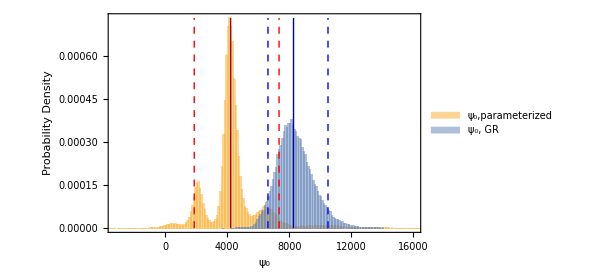

输入Mc范围：{10,100}

输入q范围：{1,10}

m1范围：{11.487,405.769}

m2范围：{4.05769,114.87}

原始数据量 = 245375，降采样后数据量 = 245375（采样比例 = 1.）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

原始KDE在有限先验区间内的积分值S = 1.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 5.77541×10^-6 for the integral and error estimates.

归一化后先验区间内积分值 = 1.（误差应<1e-5）

If::argbu: If called with 1 argument; between 2 and 4 arguments are expected.

已绘制等高线值：{0.0021}

等高线数量：1 条

第一条等高线的前5个边界点：{{49.6942,26.6685},{49.7156,24.9742},{46.6907,23.9093},{46.3028,23.8456},{42.5391,23.0336}}

Set::setps: contourPoints[n] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

===== 第i$382048条等高线 =====

包含闭合区域数：1

区域内总积分值：0.806188

可信水平百分比：80.6188%

==========================

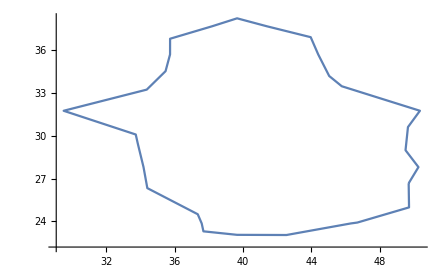

```mathematica
order=0;
n="cpsi"<>ToString[order];
compPlots[n]=PlotComparisonBetween[samples[n][n],samples[n]["psi"<>ToString[order]],Range[10,100,1],order,BCI[n]["spin1z"][[1]],BCI[n]["spin2z"][[1]]]
(*prob=0.709;*)

m1m2[n]=Transpose[{samples[n]["mass1"],samples[n]["mass2"]}];
{m1PriorRange[n],m2PriorRange[n]}=ChirpQRangeToMassRange[];
m1m2PDF[n]=GetNormalizedPDF[m1m2[n],m1PriorRange[n],m2PriorRange[n]];
(*m1m2PDF[n]=SmoothKernelDistribution[m1m2[n]]*)
contourPD[n]={0.0021};(*双峰数据密度值较低，调整为可见的等高线*)
(*0.000415*)
{contourPlotObj[n],contourPoints[n]}=GetContourPlotAndPoints[m1m2PDF[n],m1PriorRange[n],m2PriorRange[n],contourPD[n]];
contourPoints[n][[1]]=SmoothContour[contourPoints[n][[1]]];
prob=CalculateCredibleLevelsFromContours[m1m2PDF[n],contourPoints[n]][[1]][[2]];

ListLinePlot[contourPoints[[n]]]
```

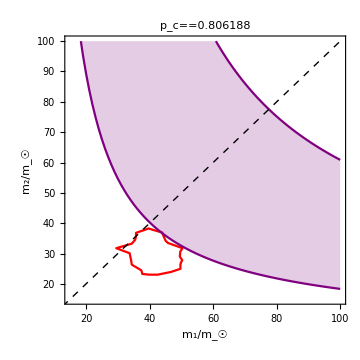

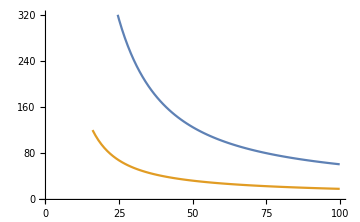

```mathematica
m1s=Range[15,100,1];
m2s=Range[15,100,1];

tapes[n]=<||>;
pInterval[n]=<||>;
pInterval[n]=IntervalFromProbability[prob];

tapeIntervals["mass1"]=Quantile[samples[n]["mass1"],pInterval[n]];
tapeIntervals["mass2"]=Quantile[samples[n]["mass2"],pInterval[n]];

Quiet[
tapeIntervals[n]=Quantile[samples[n][n],pInterval[n]];
tapes[n][n]=HypersurfacePancake[
Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals[n],{m2s},{2},
{order,BCI[n]["spin1z"][[2]],BCI[n]["spin2z"][[2]]},
tapeIntervals["mass2"],2
];
];

tapes[n]["mass1"]={{tapeIntervals["mass1"][[1]],#}&/@m2s,{tapeIntervals["mass1"][[2]],#}&/@m2s};
tapes[n]["mass2"]={{#,tapeIntervals["mass2"][[1]]}&/@m1s,{#,tapeIntervals["mass2"][[2]]}&/@m1s};

lines[n]={
(*Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[1]][[2;;]],{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],110},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[2]][[2;;]],{{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
tapes[n]["mass2"][[1]][[2;;]],
tapes[n]["mass2"][[2]][[2;;]],*)
contourPoints[n][[1]],

tapes[n][n][[1]][[2;;]],
tapes[n][n][[2]][[2;;]]
(*Select[tapes[n][n][[1]][[2;;]],Function[point,m2s[[1]]<=point[[2]]<=m2s[[-1]]]],
Select[tapes[n][n][[2]][[2;;]],Function[point,m2s[[1]]<=point[[2]]<=m2s[[-1]]]]*)
};
legends[n]=Panel[
Column[{
LineLegend[{Red,Green,Purple,Directive[Black,Dashed]},{
TraditionalForm[Row[{Subscript[m,1]}]],
TraditionalForm[Row[{Subscript[m,2]}]],
TraditionalForm[Row[{Subscript[ψ,order]}]],
TraditionalForm[Subscript[m,1]==Subscript[m,2]]},
LegendLayout->"Column"]},
Spacings->0.2,
Alignment->Left,
Frame->True,
FrameStyle->Directive[Black]
],
Background->White,
FrameMargins->0,
BaseStyle->{FontSize->13}
];

plots[n]=ListLinePlot[
lines[n],
PlotStyle->{Red,Purple,Purple},
Filling->{2->{3}},
(*FillingStyle->{HatchFilling["Diagonal"]},*)
Axes->False,
Frame->True,
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
FrameLabel->{Row[{Subscript[m,1],"/",Subscript[m,"☉"]}],Row[{Subscript[m,2],"/",Subscript[m,"☉"]}]},
FrameStyle->Directive[Black,Thickness[0.004]],
BaseStyle->{FontSize->15},
AspectRatio->1,
PlotRange->{{m1s[[1]],m1s[[-1]]},{m2s[[1]],m2s[[-1]]}},
Epilog->{
(*White,Opacity[1],Polygon[{{m1s[[-1]],m2s[[-1]]},{m1s[[1]],m2s[[-1]]},{m1s[[1]],m2s[[1]]}}],*)
Inset[
legends[n],Scaled[{0.2,0.82}],{0,0}],
Black,Dashed,Line[{{0,0},{100,100}}]
},
PlotLabel->With[{value=prob},TraditionalForm[HoldForm[Subscript[p,"c"]==value]]],
ImageSize->Medium]

ListLinePlot[{tapes[n][n][[1]][[2;;]],tapes[n][n][[2]][[2;;]]}]
```

### 2/2PN

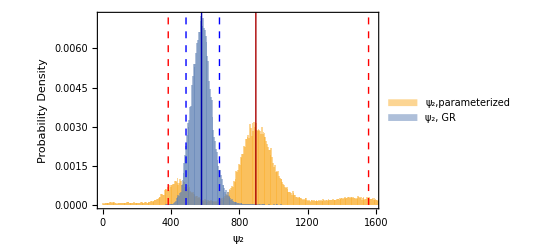

输入Mc范围：{10,100}

输入q范围：{1,10}

m1范围：{11.487,405.769}

m2范围：{4.05769,114.87}

原始数据量 = 144282，降采样后数据量 = 144282（采样比例 = 1.）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

原始KDE在有限先验区间内的积分值S = 0.999986

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 5.19092×10^-6 for the integral and error estimates.

归一化后先验区间内积分值 = 1.（误差应<1e-5）

If::argbu: If called with 1 argument; between 2 and 4 arguments are expected.

已绘制等高线值：{0.00223}

等高线数量：1 条

第一条等高线的前5个边界点：{{46.7828,25.8502},{46.7962,25.7947},{46.6907,25.6142},{43.884,23.8456},{41.7319,23.2604}}

Set::setps: contourPoints[n] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

===== 第i$420234条等高线 =====

包含闭合区域数：1

区域内总积分值：0.632803

可信水平百分比：63.2803%

==========================

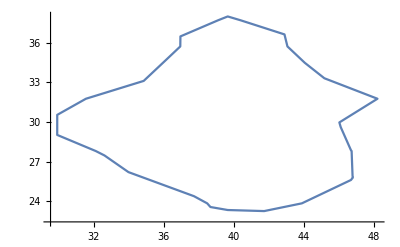

```mathematica
order=2;
n="cpsi"<>ToString[order];
compPlots[n]=PlotComparisonBetween[samples[n][n],samples[n]["psi"<>ToString[order]],Range[10,100,1],order,BCI[n]["spin1z"][[1]],BCI[n]["spin2z"][[1]]]
(*prob=0.709;*)

m1m2[n]=Transpose[{samples[n]["mass1"],samples[n]["mass2"]}];
{m1PriorRange[n],m2PriorRange[n]}=ChirpQRangeToMassRange[];
m1m2PDF[n]=GetNormalizedPDF[m1m2[n],m1PriorRange[n],m2PriorRange[n]];
(*m1m2PDF[n]=SmoothKernelDistribution[m1m2[n]]*)
contourPD[n]={0.00223};(*双峰数据密度值较低，调整为可见的等高线*)
(*0.000415*)
{contourPlotObj[n],contourPoints[n]}=GetContourPlotAndPoints[m1m2PDF[n],m1PriorRange[n],m2PriorRange[n],contourPD[n]];
contourPoints[n][[1]]=SmoothContour[contourPoints[n][[1]]];
prob=CalculateCredibleLevelsFromContours[m1m2PDF[n],contourPoints[n]][[1]][[2]];

ListLinePlot[contourPoints[[n]]]
```

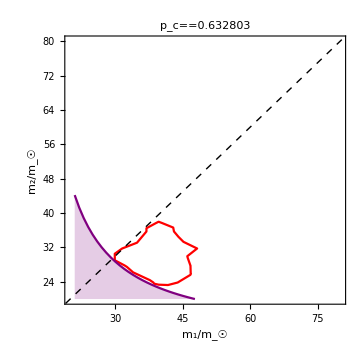

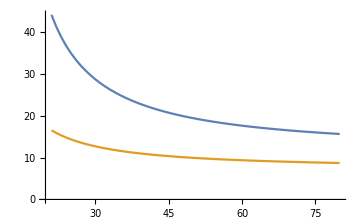

```mathematica
(*prob=0.3*)
m1s=Range[20,80,1];
m2s=Range[20,80,1];

tapes[n]=<||>;
pInterval[n]=<||>;
pInterval[n]=IntervalFromProbability[prob];

tapeIntervals["mass1"]=Quantile[samples[n]["mass1"],pInterval[n]];
tapeIntervals["mass2"]=Quantile[samples[n]["mass2"],pInterval[n]];

Quiet[
tapeIntervals[n]=Quantile[samples[n][n],pInterval[n]];
tapes[n][n]=HypersurfacePancake[
Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals[n],{m2s},{2},
{order,BCI[n]["spin1z"][[2]],BCI[n]["spin2z"][[2]]},
tapeIntervals["mass2"],2
];
];

tapes[n]["mass1"]={{tapeIntervals["mass1"][[1]],#}&/@m2s,{tapeIntervals["mass1"][[2]],#}&/@m2s};
tapes[n]["mass2"]={{#,tapeIntervals["mass2"][[1]]}&/@m1s,{#,tapeIntervals["mass2"][[2]]}&/@m1s};

lines[n]={
(*Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[1]][[2;;]],{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],110},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[2]][[2;;]],{{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
tapes[n]["mass2"][[1]][[2;;]],
tapes[n]["mass2"][[2]][[2;;]],*)
contourPoints[n][[1]],

tapes[n][n][[1]][[2;;]],
tapes[n][n][[2]][[2;;]]
};
legends[n]=Panel[
Column[{
LineLegend[{Red,Green,Purple,Directive[Black,Dashed]},{
TraditionalForm[Row[{Subscript[m,1]}]],
TraditionalForm[Row[{Subscript[m,2]}]],
TraditionalForm[Row[{Subscript[ψ,order]}]],
TraditionalForm[Subscript[m,1]==Subscript[m,2]]},
LegendLayout->"Column"]},
Spacings->0.2,
Alignment->Left,
Frame->True,
FrameStyle->Directive[Black]
],
Background->White,
FrameMargins->0,
BaseStyle->{FontSize->13}
];

plots[n]=ListLinePlot[
lines[n],
PlotStyle->{Red,Purple,Purple},
Filling->{2->{3}},
(*FillingStyle->{HatchFilling["Diagonal"]},*)
Axes->False,
Frame->True,
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
FrameLabel->{Row[{Subscript[m,1],"/",Subscript[m,"☉"]}],Row[{Subscript[m,2],"/",Subscript[m,"☉"]}]},
FrameStyle->Directive[Black,Thickness[0.004]],
BaseStyle->{FontSize->15},
AspectRatio->1,
PlotRange->{{m1s[[1]],m1s[[-1]]},{m2s[[1]],m2s[[-1]]}},
Epilog->{
(*White,Opacity[1],Polygon[{{m1s[[-1]],m2s[[-1]]},{m1s[[1]],m2s[[-1]]},{m1s[[1]],m2s[[1]]}}],*)
Inset[
legends[n],Scaled[{0.2,0.82}],{0,0}],
Black,Dashed,Line[{{0,0},{100,100}}]
},
PlotLabel->With[{value=prob},TraditionalForm[HoldForm[Subscript[p,"c"]==value]]],
ImageSize->Medium]

ListLinePlot[{tapes[n][n][[1]][[2;;]],tapes[n][n][[2]][[2;;]]}]
```

### 3/2PN

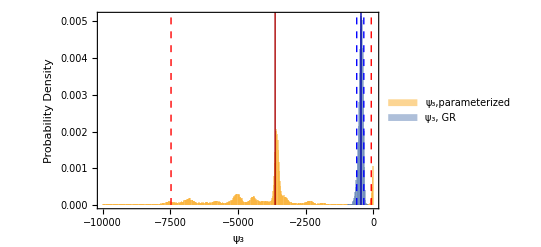

输入Mc范围：{10,100}

输入q范围：{1,10}

m1范围：{11.487,405.769}

m2范围：{4.05769,114.87}

原始数据量 = 158074，降采样后数据量 = 158074（采样比例 = 1.）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

原始KDE在有限先验区间内的积分值S = 0.999998

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 6.76643×10^-6 for the integral and error estimates.

归一化后先验区间内积分值 = 1.（误差应<1e-5）

If::argbu: If called with 1 argument; between 2 and 4 arguments are expected.

已绘制等高线值：{0.0015}

等高线数量：1 条

第一条等高线的前5个边界点：{{53.7189,27.7996},{52.7611,24.1183},{52.4603,23.8456},{51.3421,23.174},{49.7108,21.018}}

Set::setps: contourPoints[n] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

===== 第i$422451条等高线 =====

包含闭合区域数：1

区域内总积分值：0.625948

可信水平百分比：62.5948%

==========================

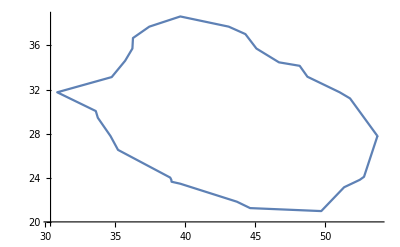

```mathematica
order=3;
n="cpsi"<>ToString[order];
compPlots[n]=PlotComparisonBetween[samples[n][n],samples[n]["psi"<>ToString[order]],Range[10,100,1],order,BCI[n]["spin1z"][[1]],BCI[n]["spin2z"][[1]]]
(*prob=0.709;*)

m1m2[n]=Transpose[{samples[n]["mass1"],samples[n]["mass2"]}];
{m1PriorRange[n],m2PriorRange[n]}=ChirpQRangeToMassRange[];
m1m2PDF[n]=GetNormalizedPDF[m1m2[n],m1PriorRange[n],m2PriorRange[n]];
(*m1m2PDF[n]=SmoothKernelDistribution[m1m2[n]]*)
contourPD[n]={0.0015};(*双峰数据密度值较低，调整为可见的等高线*)
(*0.000415*)
{contourPlotObj[n],contourPoints[n]}=GetContourPlotAndPoints[m1m2PDF[n],m1PriorRange[n],m2PriorRange[n],contourPD[n]];
contourPoints[n][[1]]=SmoothContour[contourPoints[n][[1]]];
prob=CalculateCredibleLevelsFromContours[m1m2PDF[n],contourPoints[n]][[1]][[2]];

ListLinePlot[contourPoints[[n]]]
```

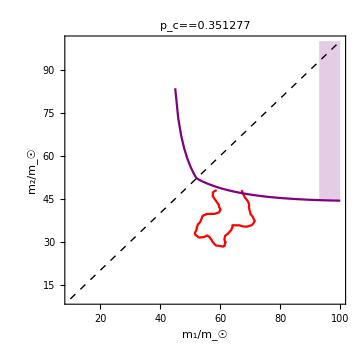

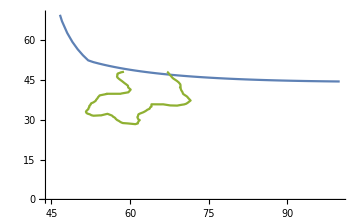

```mathematica
m1s=Range[10,100,1];
m2s=Range[10,100,1];

tapes[n]=<||>;
pInterval[n]=<||>;
pInterval[n]=IntervalFromProbability[prob];

tapeIntervals["mass1"]=Quantile[samples[n]["mass1"],pInterval[n]];
tapeIntervals["mass2"]=Quantile[samples[n]["mass2"],pInterval[n]];

Quiet[
tapeIntervals[n]=Quantile[samples[n][n],pInterval[n]];
tapes[n][n]=HypersurfacePancake[
Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals[n],{m2s},{2},
{order,BCI[n]["spin1z"][[2]],BCI[n]["spin2z"][[2]]},
tapeIntervals["mass2"],2
];
];

tapes[n]["mass1"]={{tapeIntervals["mass1"][[1]],#}&/@m2s,{tapeIntervals["mass1"][[2]],#}&/@m2s};
tapes[n]["mass2"]={{#,tapeIntervals["mass2"][[1]]}&/@m1s,{#,tapeIntervals["mass2"][[2]]}&/@m1s};

lines[n]={
(*Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[1]][[2;;]],{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],110},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[2]][[2;;]],{{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
tapes[n]["mass2"][[1]][[2;;]],
tapes[n]["mass2"][[2]][[2;;]],*)
contourPoints[n][[1]],

tapes[n][n][[1]][[2;;]],
tapes[n][n][[2]][[2;;]]
};
legends[n]=Panel[
Column[{
LineLegend[{Red,Green,Purple,Directive[Black,Dashed]},{
TraditionalForm[Row[{Subscript[m,1]}]],
TraditionalForm[Row[{Subscript[m,2]}]],
TraditionalForm[Row[{Subscript[ψ,order]}]],
TraditionalForm[Subscript[m,1]==Subscript[m,2]]},
LegendLayout->"Column"]},
Spacings->0.2,
Alignment->Left,
Frame->True,
FrameStyle->Directive[Black]
],
Background->White,
FrameMargins->0,
BaseStyle->{FontSize->13}
];

plots[n]=ListLinePlot[
lines[n],
PlotStyle->{Red,Purple,Purple},
Filling->{2->{3}},
(*FillingStyle->{HatchFilling["Diagonal"]},*)
Axes->False,
Frame->True,
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
FrameLabel->{Row[{Subscript[m,1],"/",Subscript[m,"☉"]}],Row[{Subscript[m,2],"/",Subscript[m,"☉"]}]},
FrameStyle->Directive[Black,Thickness[0.004]],
BaseStyle->{FontSize->15},
AspectRatio->1,
PlotRange->{{m1s[[1]],m1s[[-1]]},{m2s[[1]],m2s[[-1]]}},
Epilog->{
(*White,Opacity[1],Polygon[{{m1s[[-1]],m2s[[-1]]},{m1s[[1]],m2s[[-1]]},{m1s[[1]],m2s[[1]]}}],*)
Inset[
legends[n],Scaled[{0.2,0.82}],{0,0}],
Black,Dashed,Line[{{0,0},{100,100}}]
},
PlotLabel->With[{value=prob},TraditionalForm[HoldForm[Subscript[p,"c"]==value]]],
ImageSize->Medium]

ListLinePlot[{tapes[n][n][[1]][[2;;]],tapes[n][n][[2]][[2;;]],contourPoints[n][[1]]}]
```

```mathematica
contourPoints[n][[1]]
```

{{67.0649,47.999},{67.0778,47.9822},{67.1498,47.8603},{67.2618,47.6305},{67.3333,47.4854},{67.495,47.0156},{67.7654,46.4555},{67.8329,46.3148},{68.0531,45.7859},{68.2383,45.4444},{68.8943,44.5943},{68.9188,44.5561},{68.9295,44.5342},{68.9769,44.4715},{69.301,43.9413},{69.4548,43.5474},{69.5608,43.3264},{69.6071,43.035},{69.6314,42.3993},{69.5163,42.0967},{69.6445,41.788},{69.7222,41.2116},{69.818,40.867},{69.9699,40.4078},{70.0255,40.122},{70.1298,39.6372},{70.514,39.1182},{70.7669,38.8096},{70.9828,38.4075},{71.0767,38.1486},{71.5204,37.2315},{71.4891,37.1778},{71.5028,37.1159},{70.9499,36.2656},{70.6856,35.948},{70.3068,35.7083},{69.813,35.5615},{69.1776,35.3332},{68.9769,35.2621},{67.6493,35.3321},{67.6455,35.3325},{66.3171,35.7455},{65.8482,35.7313},{64.0753,35.7548},{64.0834,34.9153},{63.9139,34.7183},{63.8447,34.6317},{63.7179,34.1035},{63.6573,34.0222},{63.2606,33.672},{63.1615,33.4886},{62.8669,33.1232},{62.5387,32.776},{61.8716,32.2589},{61.591,31.9844},{61.4924,31.2579},{61.4086,31.0291},{61.3981,30.8439},{61.5873,30.0721},{61.839,29.7994},{61.6552,29.4953},{61.4676,28.787},{61.4807,28.5697},{60.9975,28.2877},{59.5387,28.5697},{58.6239,28.702},{58.3377,28.9085},{58.0944,29.1845},{57.8174,29.5589},{57.5556,29.7994},{57.2507,30.3019},{57.1988,30.5026},{57.0078,30.846},{56.7948,31.0291},{56.5921,31.4518},{56.3878,31.644},{55.6779,32.1801},{54.5646,31.644},{54.4703,31.5874},{54.2404,31.5942},{53.0181,31.4617},{52.6218,31.644},{52.3554,31.9525},{51.8655,32.2589},{51.6882,32.474},{51.5969,32.8315},{51.5721,32.9274},{51.6882,33.3525},{51.775,33.4886},{52.0325,33.9442},{52.0614,34.276},{52.2169,34.7183},{52.2031,35.0951},{52.4893,35.7036},{52.5053,35.948},{52.6008,36.141},{53.0181,36.492},{53.068,36.5629},{53.3949,37.0036},{53.4598,37.1778},{53.5113,37.4058},{53.7886,38.0512},{53.8847,38.4075},{54.1185,38.9163},{54.1846,39.0979},{55.5523,39.6372},{55.5114,39.7142},{55.6779,39.7226},{55.8282,39.7068},{58.181,39.7096},{58.3377,39.8105},{59.634,40.2521},{59.6583,40.2564},{59.6676,40.2677},{59.9425,40.867},{60.1115,41.2766},{59.92,41.5986},{59.6315,42.0967},{59.5926,42.6769},{59.5762,42.7538},{59.2086,43.3264},{58.991,43.6285},{58.425,44.5158},{58.3962,44.5561},{58.3841,44.5776},{58.3377,44.6344},{57.967,45.171},{57.7559,45.5169},{57.6041,45.7859},{57.4978,46.1742},{57.5795,46.6651},{57.5502,47.0156},{57.6648,47.3267},{58.1196,47.6305},{58.1664,47.7097},{58.3377,47.7878},{58.6914,47.9379},{58.8299,47.9989}}

```mathematica
tapes[n][n][[2]][[2;;]]
```

{{11,-17.4835+3.06885 ⅈ},{12,-19.0941+3.59178 ⅈ},{13,-20.7021+4.15322 ⅈ},{14,-22.3065+4.75302 ⅈ},{15,-23.9063+5.39108 ⅈ},{16,-25.5006+6.06731 ⅈ},{17,-27.0884+6.78166 ⅈ},{18,-28.6691+7.53405 ⅈ},{19,-30.2416+8.32446 ⅈ},{20,-31.8052+9.15284 ⅈ},{21,-33.3592+10.0192 ⅈ},{22,-34.9028+10.9234 ⅈ},{23,-36.4352+11.8656 ⅈ},{24,-37.9558+12.8456 ⅈ},{25,-39.4639+13.8635 ⅈ},{26,-40.9588+14.9192 ⅈ},{27,-42.4398+16.0127 ⅈ},{28,-43.9064+17.1439 ⅈ},{29,-45.3578+18.3128 ⅈ},{30,-46.7936+19.5194 ⅈ},{31,-48.213+20.7636 ⅈ},{32,-49.6156+22.0453 ⅈ},{33,-51.0007+23.3644 ⅈ},{34,-52.3678+24.7209 ⅈ},{35,-53.7163+26.1147 ⅈ},{36,-55.0457+27.5455 ⅈ},{37,-56.3554+29.0135 ⅈ},{38,-57.645+30.5183 ⅈ},{39,-58.9139+32.0598 ⅈ},{40,-60.1615+33.6379 ⅈ},{41,-61.3874+35.2524 ⅈ},{42,-62.5911+36.9032 ⅈ},{43,-63.772+38.59 ⅈ},{44,-64.9296+40.3126 ⅈ},{45,-66.0634+42.0709 ⅈ},{46,-67.173+43.8645 ⅈ},{47,-68.2578+45.6932 ⅈ},{48,-69.3172+47.5568 ⅈ},{49,-70.3509+49.455 ⅈ},{50,-71.3583+51.3876 ⅈ},{51,-72.3388+53.3542 ⅈ},{52,-73.292+55.3546 ⅈ},{53,-74.2174+57.3884 ⅈ},{54,-75.1144+59.4553 ⅈ},{55,-75.9825+61.555 ⅈ},{56,-76.8212+63.6872 ⅈ},{57,-77.63+65.8516 ⅈ},{58,-78.4084+68.0476 ⅈ},{59,-79.1557+70.2751 ⅈ},{60,-79.8716+72.5337 ⅈ},{61,-80.5554+74.8229 ⅈ},{62,-81.2067+77.1423 ⅈ},{63,-81.8248+79.4917 ⅈ},{64,-82.4093+81.8705 ⅈ},{65,-82.9596+84.2784 ⅈ},{66,-83.4752+86.7149 ⅈ},{67,-83.9555+89.1797 ⅈ},{68,-84.3999+91.6722 ⅈ},{69,-84.808+94.1922 ⅈ},{70,-85.1791+96.739 ⅈ},{71,-85.5128+99.3123 ⅈ},{72,-85.8084+101.912 ⅈ},{73,-86.0654+104.536 ⅈ},{74,-86.2833+107.186 ⅈ},{75,-86.4614+109.861 ⅈ},{76,-86.5992+112.559 ⅈ},{77,-86.6963+115.281 ⅈ},{78,-86.7519+118.027 ⅈ},{79,-86.7655+120.794 ⅈ},{80,-86.7367+123.584 ⅈ},{81,-86.6647+126.395 ⅈ},{82,-86.5491+129.228 ⅈ},{83,-86.3892+132.08 ⅈ},{84,-86.1846+134.953 ⅈ},{85,-85.9345+137.845 ⅈ},{86,-85.6386+140.755 ⅈ},{87,-85.2962+143.684 ⅈ},{88,-84.9067+146.631 ⅈ},{89,-84.4695+149.594 ⅈ},{90,-83.9842+152.573 ⅈ},{91,-83.4501+155.569 ⅈ},{92,-82.8666+158.579 ⅈ},{93,-82.2332+161.604 ⅈ},{94,-81.5494+164.643 ⅈ},{95,-80.8145+167.695 ⅈ},{96,-80.0279+170.759 ⅈ},{97,-79.1892+173.835 ⅈ},{98,-78.2977+176.922 ⅈ},{99,-77.3528+180.02 ⅈ},{100,-76.3541+183.127 ⅈ}}

### 4/2PN

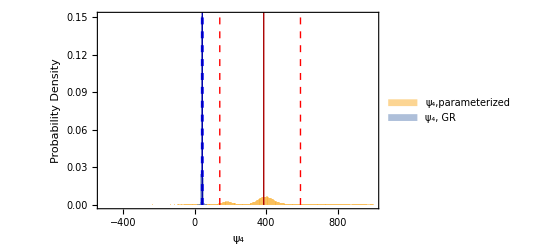

输入Mc范围：{10,100}

输入q范围：{1,10}

m1范围：{11.487,405.769}

m2范围：{4.05769,114.87}

原始数据量 = 144951，降采样后数据量 = 144951（采样比例 = 1.）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

原始KDE在有限先验区间内的积分值S = 1.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.999999 and 6.53663×10^-6 for the integral and error estimates.

归一化后先验区间内积分值 = 0.999999（误差应<1e-5）

If::argbu: If called with 1 argument; between 2 and 4 arguments are expected.

已绘制等高线值：{0.00001}

等高线数量：1 条

第一条等高线的前5个边界点：{{53.1687,43.4753},{53.7315,43.1751},{59.9761,41.4309},{66.1565,39.6759},{59.9315,37.9334}}

Set::setps: contourPoints[n] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

===== 第i$423933条等高线 =====

包含闭合区域数：1

区域内总积分值：0.998152

可信水平百分比：99.8152%

==========================

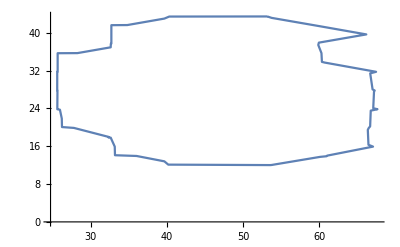

```mathematica
order=4;
n="cpsi"<>ToString[order];
compPlots[n]=PlotComparisonBetween[samples[n][n],samples[n]["psi"<>ToString[order]],Range[10,100,1],order,BCI[n]["spin1z"][[1]],BCI[n]["spin2z"][[1]]]
(*prob=0.709;*)

m1m2[n]=Transpose[{samples[n]["mass1"],samples[n]["mass2"]}];
{m1PriorRange[n],m2PriorRange[n]}=ChirpQRangeToMassRange[];
m1m2PDF[n]=GetNormalizedPDF[m1m2[n],m1PriorRange[n],m2PriorRange[n]];
(*m1m2PDF[n]=SmoothKernelDistribution[m1m2[n]]*)
contourPD[n]={0.00001};(*双峰数据密度值较低，调整为可见的等高线*)
(*0.000415*)
{contourPlotObj[n],contourPoints[n]}=GetContourPlotAndPoints[m1m2PDF[n],m1PriorRange[n],m2PriorRange[n],contourPD[n]];
contourPoints[n][[1]]=SmoothContour[contourPoints[n][[1]]];
prob=CalculateCredibleLevelsFromContours[m1m2PDF[n],contourPoints[n]][[1]][[2]];

ListLinePlot[contourPoints[[n]]]
```

0.9999

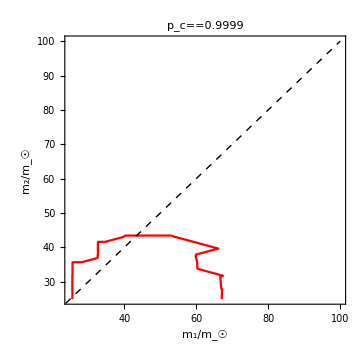

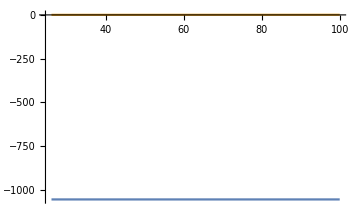

```mathematica
prob=0.9999
m1s=Range[25,100,1];
m2s=Range[25,100,1];

tapes[n]=<||>;
pInterval[n]=<||>;
pInterval[n]=IntervalFromProbability[prob];

tapeIntervals["mass1"]=Quantile[samples[n]["mass1"],pInterval[n]];
tapeIntervals["mass2"]=Quantile[samples[n]["mass2"],pInterval[n]];

Quiet[
tapeIntervals[n]=Quantile[samples[n][n],pInterval[n]];
tapes[n][n]=HypersurfacePancake[
Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals[n],{m2s},{2},
{order,BCI[n]["spin1z"][[2]],BCI[n]["spin2z"][[2]]},
tapeIntervals["mass2"],2
];
];

tapes[n]["mass1"]={{tapeIntervals["mass1"][[1]],#}&/@m2s,{tapeIntervals["mass1"][[2]],#}&/@m2s};
tapes[n]["mass2"]={{#,tapeIntervals["mass2"][[1]]}&/@m1s,{#,tapeIntervals["mass2"][[2]]}&/@m1s};

lines[n]={
(*Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[1]][[2;;]],{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],110},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[2]][[2;;]],{{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
tapes[n]["mass2"][[1]][[2;;]],
tapes[n]["mass2"][[2]][[2;;]],*)
contourPoints[n][[1]],

tapes[n][n][[1]][[2;;]],
tapes[n][n][[2]][[2;;]]
};
legends[n]=Panel[
Column[{
LineLegend[{Red,Green,Purple,Directive[Black,Dashed]},{
TraditionalForm[Row[{Subscript[m,1]}]],
TraditionalForm[Row[{Subscript[m,2]}]],
TraditionalForm[Row[{Subscript[ψ,order]}]],
TraditionalForm[Subscript[m,1]==Subscript[m,2]]},
LegendLayout->"Column"]},
Spacings->0.2,
Alignment->Left,
Frame->True,
FrameStyle->Directive[Black]
],
Background->White,
FrameMargins->0,
BaseStyle->{FontSize->13}
];

plots[n]=ListLinePlot[
lines[n],
PlotStyle->{Red,Purple,Purple},
Filling->{2->{3}},
(*FillingStyle->{HatchFilling["Diagonal"]},*)
Axes->False,
Frame->True,
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
FrameLabel->{Row[{Subscript[m,1],"/",Subscript[m,"☉"]}],Row[{Subscript[m,2],"/",Subscript[m,"☉"]}]},
FrameStyle->Directive[Black,Thickness[0.004]],
BaseStyle->{FontSize->15},
AspectRatio->1,
PlotRange->{{m1s[[1]],m1s[[-1]]},{m2s[[1]],m2s[[-1]]}},
Epilog->{
(*White,Opacity[1],Polygon[{{m1s[[-1]],m2s[[-1]]},{m1s[[1]],m2s[[-1]]},{m1s[[1]],m2s[[1]]}}],*)
Inset[
legends[n],Scaled[{0.2,0.82}],{0,0}],
Black,Dashed,Line[{{0,0},{100,100}}]
},
PlotLabel->With[{value=prob},TraditionalForm[HoldForm[Subscript[p,"c"]==value]]],
ImageSize->Medium]

ListLinePlot[{tapes[n][n][[1]][[2;;]],tapes[n][n][[2]][[2;;]]}]
```

```mathematica
tapes[n][n][[2]][[2;;]]
```

{{16,4446.34},{17,4872.4},{18,5311.35},{19,5762.81},{20,6226.45},{21,6701.97},{22,7189.07},{23,7687.5},{24,8197.},{25,8717.34},{26,9248.3},{27,9789.67},{28,10341.3},{29,10902.9},{30,11474.4},{31,12055.6},{32,12646.3},{33,13246.4},{34,13855.7},{35,14474.2},{36,15101.6},{37,15737.9},{38,16382.9},{39,17036.5},{40,17698.6},{41,18369.2},{42,19048.},{43,19735.},{44,20430.1},{45,21133.2},{46,21844.2},{47,22563.1},{48,23289.7},{49,24023.9},{50,24765.8},{51,25515.1},{52,26271.9},{53,27036.1},{54,27807.5},{55,28586.2},{56,29372.},{57,30164.9},{58,30964.9},{59,31771.8},{60,32585.7},{61,33406.4},{62,34233.8},{63,35068.1},{64,35909.},{65,36756.6},{66,37610.7},{67,38471.4},{68,39338.6},{69,40212.2},{70,41092.2},{71,41978.5},{72,42871.2},{73,43770.1},{74,44675.2},{75,45586.5},{76,46503.9},{77,47427.5},{78,48357.},{79,49292.6},{80,50234.2},{81,51181.6},{82,52135.},{83,53094.3},{84,54059.4},{85,55030.2},{86,56006.9},{87,56989.2},{88,57977.3},{89,58971.},{90,59970.3},{91,60975.2},{92,61985.7},{93,63001.8},{94,64023.3},{95,65050.3},{96,66082.8},{97,67120.7},{98,68164.},{99,69212.6},{100,70266.6}}

### 5/2PN, log

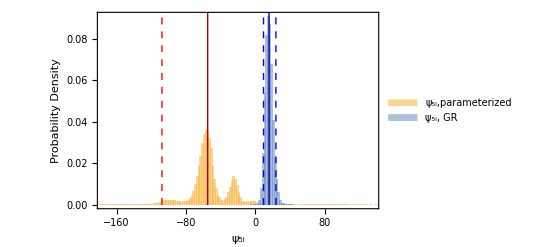

输入Mc范围：{10,100}

输入q范围：{1,10}

m1范围：{11.487,405.769}

m2范围：{4.05769,114.87}

原始数据量 = 155140，降采样后数据量 = 155140（采样比例 = 1.）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

原始KDE在有限先验区间内的积分值S = 0.999999

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 9.2158×10^-6 for the integral and error estimates.

归一化后先验区间内积分值 = 1.（误差应<1e-5）

If::argbu: If called with 1 argument; between 2 and 4 arguments are expected.

已绘制等高线值：{0.0001}

等高线数量：1 条

第一条等高线的前5个边界点：{{52.0279,43.1547},{52.4647,40.0319},{52.9893,39.6759},{53.1936,39.5247},{53.4243,37.6971}}

Set::setps: contourPoints[n] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

===== 第i$433001条等高线 =====

包含闭合区域数：1

区域内总积分值：0.987923

可信水平百分比：98.7923%

==========================

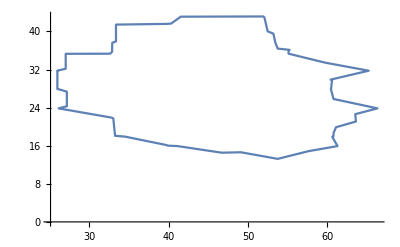

```mathematica
order="5l";
n="cpsi"<>ToString[order];
compPlots[n]=PlotComparisonBetween[samples[n][n],samples[n]["psi"<>ToString[order]],Range[10,100,1],order,BCI[n]["spin1z"][[1]],BCI[n]["spin2z"][[1]]]
(*prob=0.709;*)

m1m2[n]=Transpose[{samples[n]["mass1"],samples[n]["mass2"]}];
{m1PriorRange[n],m2PriorRange[n]}=ChirpQRangeToMassRange[];
m1m2PDF[n]=GetNormalizedPDF[m1m2[n],m1PriorRange[n],m2PriorRange[n]];
(*m1m2PDF[n]=SmoothKernelDistribution[m1m2[n]]*)
contourPD[n]={0.0001};(*双峰数据密度值较低，调整为可见的等高线*)
(*0.000415*)
{contourPlotObj[n],contourPoints[n]}=GetContourPlotAndPoints[m1m2PDF[n],m1PriorRange[n],m2PriorRange[n],contourPD[n]];
contourPoints[n][[1]]=SmoothContour[contourPoints[n][[1]]];
prob=CalculateCredibleLevelsFromContours[m1m2PDF[n],contourPoints[n]][[1]][[2]];

ListLinePlot[contourPoints[[n]]]
```

0.874

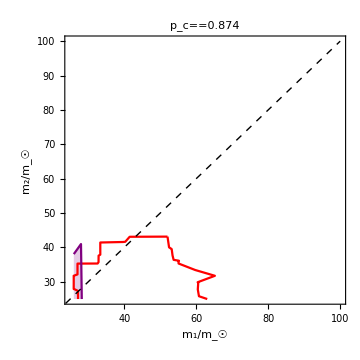

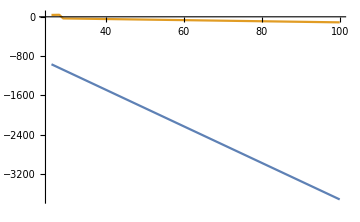

```mathematica
prob=0.874
m1s=Range[25,100,1];
m2s=Range[25,100,1];

tapes[n]=<||>;
pInterval[n]=<||>;
pInterval[n]=IntervalFromProbability[prob];

tapeIntervals["mass1"]=Quantile[samples[n]["mass1"],pInterval[n]];
tapeIntervals["mass2"]=Quantile[samples[n]["mass2"],pInterval[n]];

Quiet[
tapeIntervals[n]=Quantile[samples[n][n],pInterval[n]];
tapes[n][n]=HypersurfacePancake[
Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals[n],{m2s},{2},
{order,BCI[n]["spin1z"][[2]],BCI[n]["spin2z"][[2]]},
tapeIntervals["mass2"],2
];
];

tapes[n]["mass1"]={{tapeIntervals["mass1"][[1]],#}&/@m2s,{tapeIntervals["mass1"][[2]],#}&/@m2s};
tapes[n]["mass2"]={{#,tapeIntervals["mass2"][[1]]}&/@m1s,{#,tapeIntervals["mass2"][[2]]}&/@m1s};

lines[n]={
(*Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[1]][[2;;]],{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],110},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[2]][[2;;]],{{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
tapes[n]["mass2"][[1]][[2;;]],
tapes[n]["mass2"][[2]][[2;;]],*)
contourPoints[n][[1]],

tapes[n][n][[1]][[2;;]],
tapes[n][n][[2]][[2;;]]
};
legends[n]=Panel[
Column[{
LineLegend[{Red,Green,Purple,Directive[Black,Dashed]},{
TraditionalForm[Row[{Subscript[m,1]}]],
TraditionalForm[Row[{Subscript[m,2]}]],
TraditionalForm[Row[{Subscript[ψ,order]}]],
TraditionalForm[Subscript[m,1]==Subscript[m,2]]},
LegendLayout->"Column"]},
Spacings->0.2,
Alignment->Left,
Frame->True,
FrameStyle->Directive[Black]
],
Background->White,
FrameMargins->0,
BaseStyle->{FontSize->13}
];

plots[n]=ListLinePlot[
lines[n],
PlotStyle->{Red,Purple,Purple},
Filling->{2->{3}},
(*FillingStyle->{HatchFilling["Diagonal"]},*)
Axes->False,
Frame->True,
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
FrameLabel->{Row[{Subscript[m,1],"/",Subscript[m,"☉"]}],Row[{Subscript[m,2],"/",Subscript[m,"☉"]}]},
FrameStyle->Directive[Black,Thickness[0.004]],
BaseStyle->{FontSize->15},
AspectRatio->1,
PlotRange->{{m1s[[1]],m1s[[-1]]},{m2s[[1]],m2s[[-1]]}},
Epilog->{
(*White,Opacity[1],Polygon[{{m1s[[-1]],m2s[[-1]]},{m1s[[1]],m2s[[-1]]},{m1s[[1]],m2s[[1]]}}],*)
Inset[
legends[n],Scaled[{0.2,0.82}],{0,0}],
Black,Dashed,Line[{{0,0},{100,100}}]
},
PlotLabel->With[{value=prob},TraditionalForm[HoldForm[Subscript[p,"c"]==value]]],
ImageSize->Medium]

ListLinePlot[{tapes[n][n][[1]][[2;;]],tapes[n][n][[2]][[2;;]]}]
```

### 6/2PN

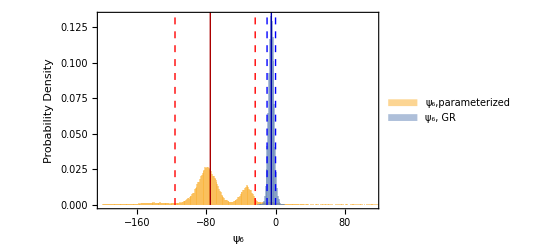

输入Mc范围：{10,100}

输入q范围：{1,10}

m1范围：{11.487,405.769}

m2范围：{4.05769,114.87}

原始数据量 = 147945，降采样后数据量 = 147945（采样比例 = 1.）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

原始KDE在有限先验区间内的积分值S = 0.999999

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 7.1139×10^-6 for the integral and error estimates.

归一化后先验区间内积分值 = 1.（误差应<1e-5）

If::argbu: If called with 1 argument; between 2 and 4 arguments are expected.

已绘制等高线值：{0.0001}

等高线数量：1 条

第一条等高线的前5个边界点：{{48.1324,42.0598},{48.8776,41.0401},{52.6973,39.6759},{53.1987,39.5261},{53.7315,37.8794}}

Set::setps: contourPoints[n] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

===== 第i$441538条等高线 =====

包含闭合区域数：1

区域内总积分值：0.987403

可信水平百分比：98.7403%

==========================

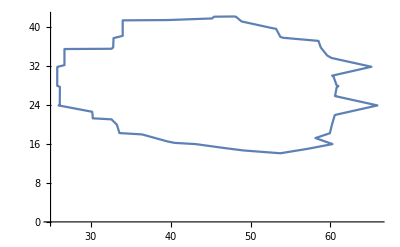

```mathematica
order=6;
n="cpsi"<>ToString[order];
compPlots[n]=PlotComparisonBetween[samples[n][n],samples[n]["psi"<>ToString[order]],Range[10,100,1],order,BCI[n]["spin1z"][[1]],BCI[n]["spin2z"][[1]]]
(*prob=0.709;*)

m1m2[n]=Transpose[{samples[n]["mass1"],samples[n]["mass2"]}];
{m1PriorRange[n],m2PriorRange[n]}=ChirpQRangeToMassRange[];
m1m2PDF[n]=GetNormalizedPDF[m1m2[n],m1PriorRange[n],m2PriorRange[n]];
(*m1m2PDF[n]=SmoothKernelDistribution[m1m2[n]]*)
contourPD[n]={0.0001};(*双峰数据密度值较低，调整为可见的等高线*)
(*0.000415*)
{contourPlotObj[n],contourPoints[n]}=GetContourPlotAndPoints[m1m2PDF[n],m1PriorRange[n],m2PriorRange[n],contourPD[n]];
contourPoints[n][[1]]=SmoothContour[contourPoints[n][[1]]];
prob=CalculateCredibleLevelsFromContours[m1m2PDF[n],contourPoints[n]][[1]][[2]];

ListLinePlot[contourPoints[[n]]]
```

0.99

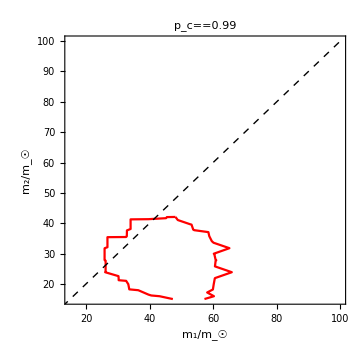

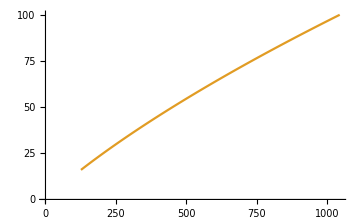

```mathematica
prob=0.99
m1s=Range[15,100,1];
m2s=Range[15,100,1];

tapes[n]=<||>;
pInterval[n]=<||>;
pInterval[n]=IntervalFromProbability[prob];

tapeIntervals["mass1"]=Quantile[samples[n]["mass1"],pInterval[n]];
tapeIntervals["mass2"]=Quantile[samples[n]["mass2"],pInterval[n]];

Quiet[
tapeIntervals[n]=Quantile[samples[n][n],pInterval[n]];
tapes[n][n]=HypersurfacePancake[
Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals[n],{m2s},{2},
{order,BCI[n]["spin1z"][[2]],BCI[n]["spin2z"][[2]]},
tapeIntervals["mass2"],2
];
];

tapes[n]["mass1"]={{tapeIntervals["mass1"][[1]],#}&/@m2s,{tapeIntervals["mass1"][[2]],#}&/@m2s};
tapes[n]["mass2"]={{#,tapeIntervals["mass2"][[1]]}&/@m1s,{#,tapeIntervals["mass2"][[2]]}&/@m1s};

lines[n]={
(*Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[1]][[2;;]],{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],110},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[2]][[2;;]],{{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
tapes[n]["mass2"][[1]][[2;;]],
tapes[n]["mass2"][[2]][[2;;]],*)
contourPoints[n][[1]],

Reverse/@tapes[n][n][[1]][[2;;]],
Reverse/@tapes[n][n][[2]][[2;;]]
};
legends[n]=Panel[
Column[{
LineLegend[{Red,Green,Purple,Directive[Black,Dashed]},{
TraditionalForm[Row[{Subscript[m,1]}]],
TraditionalForm[Row[{Subscript[m,2]}]],
TraditionalForm[Row[{Subscript[ψ,order]}]],
TraditionalForm[Subscript[m,1]==Subscript[m,2]]},
LegendLayout->"Column"]},
Spacings->0.2,
Alignment->Left,
Frame->True,
FrameStyle->Directive[Black]
],
Background->White,
FrameMargins->0,
BaseStyle->{FontSize->13}
];

plots[n]=ListLinePlot[
lines[n],
PlotStyle->{Red,Purple,Purple},
Filling->{2->{3}},
(*FillingStyle->{HatchFilling["Diagonal"]},*)
Axes->False,
Frame->True,
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
FrameLabel->{Row[{Subscript[m,1],"/",Subscript[m,"☉"]}],Row[{Subscript[m,2],"/",Subscript[m,"☉"]}]},
FrameStyle->Directive[Black,Thickness[0.004]],
BaseStyle->{FontSize->15},
AspectRatio->1,
PlotRange->{{m1s[[1]],m1s[[-1]]},{m2s[[1]],m2s[[-1]]}},
Epilog->{
(*White,Opacity[1],Polygon[{{m1s[[-1]],m2s[[-1]]},{m1s[[1]],m2s[[-1]]},{m1s[[1]],m2s[[1]]}}],*)
Inset[
legends[n],Scaled[{0.2,0.82}],{0,0}],
Black,Dashed,Line[{{0,0},{100,100}}]
},
PlotLabel->With[{value=prob},TraditionalForm[HoldForm[Subscript[p,"c"]==value]]],
ImageSize->Medium]

ListLinePlot[{Reverse/@tapes[n][n][[1]][[2;;]],Reverse/@tapes[n][n][[2]][[2;;]]}]
```

```mathematica
Reverse/@tapes[n][n][[2]][[2;;]]
```

{{181.289,6},{195.811,7},{209.338,8},{222.043,9},{234.052,10},{245.462,11},{256.349,12},{266.774,13},{276.786,14},{286.427,15},{295.731,16},{304.727,17},{313.44,18},{321.893,19},{330.105,20},{338.092,21},{345.87,22},{353.451,23},{360.848,24},{368.072,25},{375.131,26},{382.035,27},{388.793,28},{395.41,29},{401.894,30},{408.252,31},{414.488,32},{420.609,33},{426.618,34},{432.521,35},{438.322,36},{444.025,37},{449.633,38},{455.15,39},{460.58,40},{465.925,41},{471.188,42},{476.371,43},{481.479,44},{486.512,45},{491.473,46},{496.365,47},{501.189,48},{505.947,49},{510.642,50},{515.275,51},{519.847,52},{524.361,53},{528.818,54},{533.218,55},{537.565,56},{541.859,57},{546.101,58},{550.293,59},{554.436,60},{558.53,61},{562.578,62},{566.579,63},{570.536,64},{574.449,65},{578.319,66},{582.147,67},{585.934,68},{589.68,69},{593.387,70},{597.055,71},{600.684,72},{604.277,73},{607.833,74},{611.354,75},{614.839,76},{618.289,77},{621.705,78},{625.089,79},{628.439,80},{631.757,81},{635.043,82},{638.299,83},{641.524,84},{644.718,85},{647.883,86},{651.019,87},{654.126,88},{657.206,89},{660.257,90},{663.281,91},{666.278,92},{669.248,93},{672.192,94},{675.111,95},{678.004,96},{680.872,97},{683.715,98},{686.534,99},{689.329,100}}

### 6/2PN, log

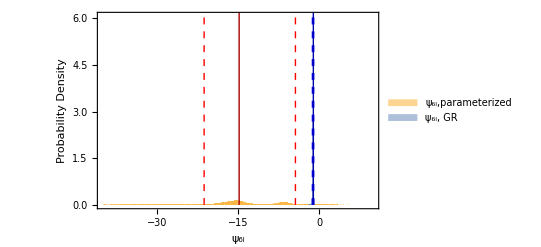

输入Mc范围：{10,100}

输入q范围：{1,10}

m1范围：{11.487,405.769}

m2范围：{4.05769,114.87}

原始数据量 = 144312，降采样后数据量 = 144312（采样比例 = 1.）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

原始KDE在有限先验区间内的积分值S = 1.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 0.0000102885 for the integral and error estimates.

归一化后先验区间内积分值 = 1.（误差应<1e-5）

If::argbu: If called with 1 argument; between 2 and 4 arguments are expected.

已绘制等高线值：{0.00002}

等高线数量：1 条

第一条等高线的前5个边界点：{{60.2629,14.0948},{53.7315,12.1594},{52.1416,12.4197},{42.5189,12.7792},{39.65,13.0246}}

Set::setps: contourPoints[n] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

===== 第i$445380条等高线 =====

包含闭合区域数：1

区域内总积分值：0.997715

可信水平百分比：99.7715%

==========================

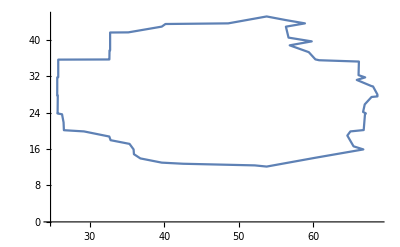

```mathematica
order="6l";
n="cpsi"<>ToString[order];
compPlots[n]=PlotComparisonBetween[samples[n][n],samples[n]["psi"<>ToString[order]],Range[10,100,1],order,BCI[n]["spin1z"][[1]],BCI[n]["spin2z"][[1]]]
(*prob=0.709;*)

m1m2[n]=Transpose[{samples[n]["mass1"],samples[n]["mass2"]}];
{m1PriorRange[n],m2PriorRange[n]}=ChirpQRangeToMassRange[];
m1m2PDF[n]=GetNormalizedPDF[m1m2[n],m1PriorRange[n],m2PriorRange[n]];
(*m1m2PDF[n]=SmoothKernelDistribution[m1m2[n]]*)
contourPD[n]={0.00002};(*双峰数据密度值较低，调整为可见的等高线*)
(*0.000415*)
{contourPlotObj[n],contourPoints[n]}=GetContourPlotAndPoints[m1m2PDF[n],m1PriorRange[n],m2PriorRange[n],contourPD[n]];
contourPoints[n][[1]]=SmoothContour[contourPoints[n][[1]]];
prob=CalculateCredibleLevelsFromContours[m1m2PDF[n],contourPoints[n]][[1]][[2]];

ListLinePlot[contourPoints[[n]]]
```

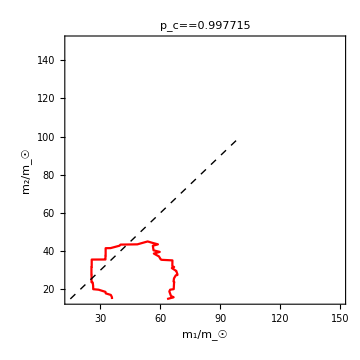

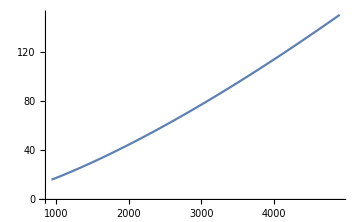

```mathematica
(*prob=0.98*)
m1s=Range[15,150,1];
m2s=Range[15,150,1];

tapes[n]=<||>;
pInterval[n]=<||>;
pInterval[n]=IntervalFromProbability[prob];

tapeIntervals["mass1"]=Quantile[samples[n]["mass1"],pInterval[n]];
tapeIntervals["mass2"]=Quantile[samples[n]["mass2"],pInterval[n]];

Quiet[
tapeIntervals[n]=Quantile[samples[n][n],pInterval[n]];
tapes[n][n]=HypersurfacePancake[
Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals[n],{m2s},{2},
{order,BCI[n]["spin1z"][[2]],BCI[n]["spin2z"][[2]]},
tapeIntervals["mass2"],2
];
];

tapes[n]["mass1"]={{tapeIntervals["mass1"][[1]],#}&/@m2s,{tapeIntervals["mass1"][[2]],#}&/@m2s};
tapes[n]["mass2"]={{#,tapeIntervals["mass2"][[1]]}&/@m1s,{#,tapeIntervals["mass2"][[2]]}&/@m1s};

lines[n]={
(*Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[1]][[2;;]],{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],110},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[2]][[2;;]],{{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
tapes[n]["mass2"][[1]][[2;;]],
tapes[n]["mass2"][[2]][[2;;]],*)
contourPoints[n][[1]],

Reverse/@tapes[n][n][[1]][[2;;]],
Reverse/@tapes[n][n][[2]][[2;;]]
};
legends[n]=Panel[
Column[{
LineLegend[{Red,Green,Purple,Directive[Black,Dashed]},{
TraditionalForm[Row[{Subscript[m,1]}]],
TraditionalForm[Row[{Subscript[m,2]}]],
TraditionalForm[Row[{Subscript[ψ,order]}]],
TraditionalForm[Subscript[m,1]==Subscript[m,2]]},
LegendLayout->"Column"]},
Spacings->0.2,
Alignment->Left,
Frame->True,
FrameStyle->Directive[Black]
],
Background->White,
FrameMargins->0,
BaseStyle->{FontSize->13}
];

plots[n]=ListLinePlot[
lines[n],
PlotStyle->{Red,Purple,Purple},
Filling->{2->{3}},
(*FillingStyle->{HatchFilling["Diagonal"]},*)
Axes->False,
Frame->True,
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
FrameLabel->{Row[{Subscript[m,1],"/",Subscript[m,"☉"]}],Row[{Subscript[m,2],"/",Subscript[m,"☉"]}]},
FrameStyle->Directive[Black,Thickness[0.004]],
BaseStyle->{FontSize->15},
AspectRatio->1,
PlotRange->{{m1s[[1]],m1s[[-1]]},{m2s[[1]],m2s[[-1]]}},
Epilog->{
(*White,Opacity[1],Polygon[{{m1s[[-1]],m2s[[-1]]},{m1s[[1]],m2s[[-1]]},{m1s[[1]],m2s[[1]]}}],*)
Inset[
legends[n],Scaled[{0.2,0.82}],{0,0}],
Black,Dashed,Line[{{0,0},{100,100}}]
},
PlotLabel->With[{value=prob},TraditionalForm[HoldForm[Subscript[p,"c"]==value]]],
ImageSize->Medium]

ListLinePlot[{Reverse/@tapes[n][n][[1]][[2;;]],Reverse/@tapes[n][n][[2]][[2;;]]}]
```

```mathematica
Plot[m1m2[n]]
```

Plot::argr: Plot called with 1 argument; 2 arguments are expected.

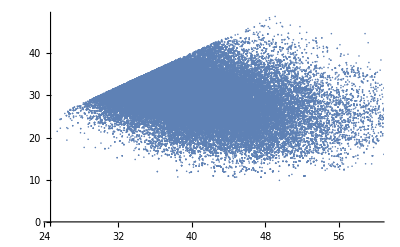

```mathematica
ListPlot[m1m2[n]]
```

### 7/2PN

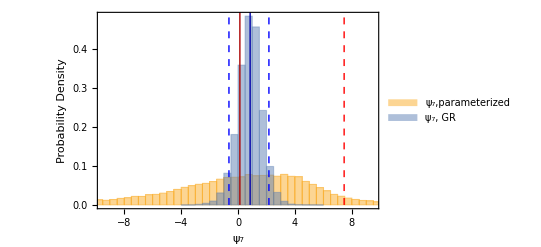

输入Mc范围：{10,100}

输入q范围：{1,10}

m1范围：{11.487,405.769}

m2范围：{4.05769,114.87}

原始数据量 = 147419，降采样后数据量 = 147419（采样比例 = 1.）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

原始KDE在有限先验区间内的积分值S = 0.999997

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 0.0000103175 for the integral and error estimates.

归一化后先验区间内积分值 = 1.（误差应<1e-5）

If::argbu: If called with 1 argument; between 2 and 4 arguments are expected.

已绘制等高线值：{0.007}

等高线数量：0 条

Part::partw: Part 1 of {} does not exist.

Set::setps: contourPoints[n] in the part assignment is not a symbol.

===== 第i$455486条等高线 =====

包含闭合区域数：0

区域内总积分值：0.

可信水平百分比：0.%

==========================

-Graphics-

```mathematica
order=7;
n="cpsi"<>ToString[order];
compPlots[n]=PlotComparisonBetween[samples[n][n],samples[n]["psi"<>ToString[order]],Range[10,100,1],order,BCI[n]["spin1z"][[1]],BCI[n]["spin2z"][[1]]]
(*prob=0.709;*)

m1m2[n]=Transpose[{samples[n]["mass1"],samples[n]["mass2"]}];
{m1PriorRange[n],m2PriorRange[n]}=ChirpQRangeToMassRange[];
m1m2PDF[n]=GetNormalizedPDF[m1m2[n],m1PriorRange[n],m2PriorRange[n]];
(*m1m2PDF[n]=SmoothKernelDistribution[m1m2[n]]*)
contourPD[n]={0.007};(*双峰数据密度值较低，调整为可见的等高线*)
(*0.000415*)
{contourPlotObj[n],contourPoints[n]}=GetContourPlotAndPoints[m1m2PDF[n],m1PriorRange[n],m2PriorRange[n],contourPD[n]];
contourPoints[n][[1]]=SmoothContour[contourPoints[n][[1]]];
prob=CalculateCredibleLevelsFromContours[m1m2PDF[n],contourPoints[n]][[1]][[2]];

ListLinePlot[contourPoints[[n]]]
```

0.1

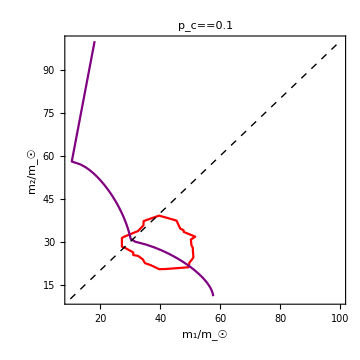

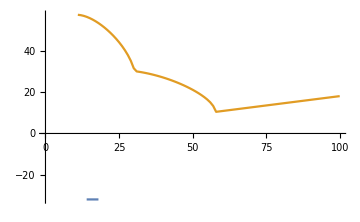

```mathematica
prob=0.1
m1s=Range[10,100,1];
m2s=Range[10,100,1];

tapes[n]=<||>;
pInterval[n]=<||>;
pInterval[n]=IntervalFromProbability[prob];

tapeIntervals["mass1"]=Quantile[samples[n]["mass1"],pInterval[n]];
tapeIntervals["mass2"]=Quantile[samples[n]["mass2"],pInterval[n]];

Quiet[
tapeIntervals[n]=Quantile[samples[n][n],pInterval[n]];
tapes[n][n]=HypersurfacePancake[
Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals[n],{m2s},{2},
{order,BCI[n]["spin1z"][[2]],BCI[n]["spin2z"][[2]]},
tapeIntervals["mass2"],2
];
];

tapes[n]["mass1"]={{tapeIntervals["mass1"][[1]],#}&/@m2s,{tapeIntervals["mass1"][[2]],#}&/@m2s};
tapes[n]["mass2"]={{#,tapeIntervals["mass2"][[1]]}&/@m1s,{#,tapeIntervals["mass2"][[2]]}&/@m1s};

lines[n]={
(*Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[1]][[2;;]],{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],110},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[2]][[2;;]],{{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
tapes[n]["mass2"][[1]][[2;;]],
tapes[n]["mass2"][[2]][[2;;]],*)
contourPoints[n][[1]],

Reverse/@tapes[n][n][[1]][[2;;]],
Reverse/@tapes[n][n][[2]][[2;;]]
};
legends[n]=Panel[
Column[{
LineLegend[{Red,Green,Purple,Directive[Black,Dashed]},{
TraditionalForm[Row[{Subscript[m,1]}]],
TraditionalForm[Row[{Subscript[m,2]}]],
TraditionalForm[Row[{Subscript[ψ,order]}]],
TraditionalForm[Subscript[m,1]==Subscript[m,2]]},
LegendLayout->"Column"]},
Spacings->0.2,
Alignment->Left,
Frame->True,
FrameStyle->Directive[Black]
],
Background->White,
FrameMargins->0,
BaseStyle->{FontSize->13}
];

plots[n]=ListLinePlot[
lines[n],
PlotStyle->{Red,Purple,Purple},
Filling->{2->{3}},
(*FillingStyle->{HatchFilling["Diagonal"]},*)
Axes->False,
Frame->True,
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
FrameLabel->{Row[{Subscript[m,1],"/",Subscript[m,"☉"]}],Row[{Subscript[m,2],"/",Subscript[m,"☉"]}]},
FrameStyle->Directive[Black,Thickness[0.004]],
BaseStyle->{FontSize->15},
AspectRatio->1,
PlotRange->{{m1s[[1]],m1s[[-1]]},{m2s[[1]],m2s[[-1]]}},
Epilog->{
(*White,Opacity[1],Polygon[{{m1s[[-1]],m2s[[-1]]},{m1s[[1]],m2s[[-1]]},{m1s[[1]],m2s[[1]]}}],*)
Inset[
legends[n],Scaled[{0.2,0.82}],{0,0}],
Black,Dashed,Line[{{0,0},{100,100}}]
},
PlotLabel->With[{value=prob},TraditionalForm[HoldForm[Subscript[p,"c"]==value]]],
ImageSize->Medium]

ListLinePlot[{tapes[n][n][[1]][[2;;]],tapes[n][n][[2]][[2;;]]}]
```

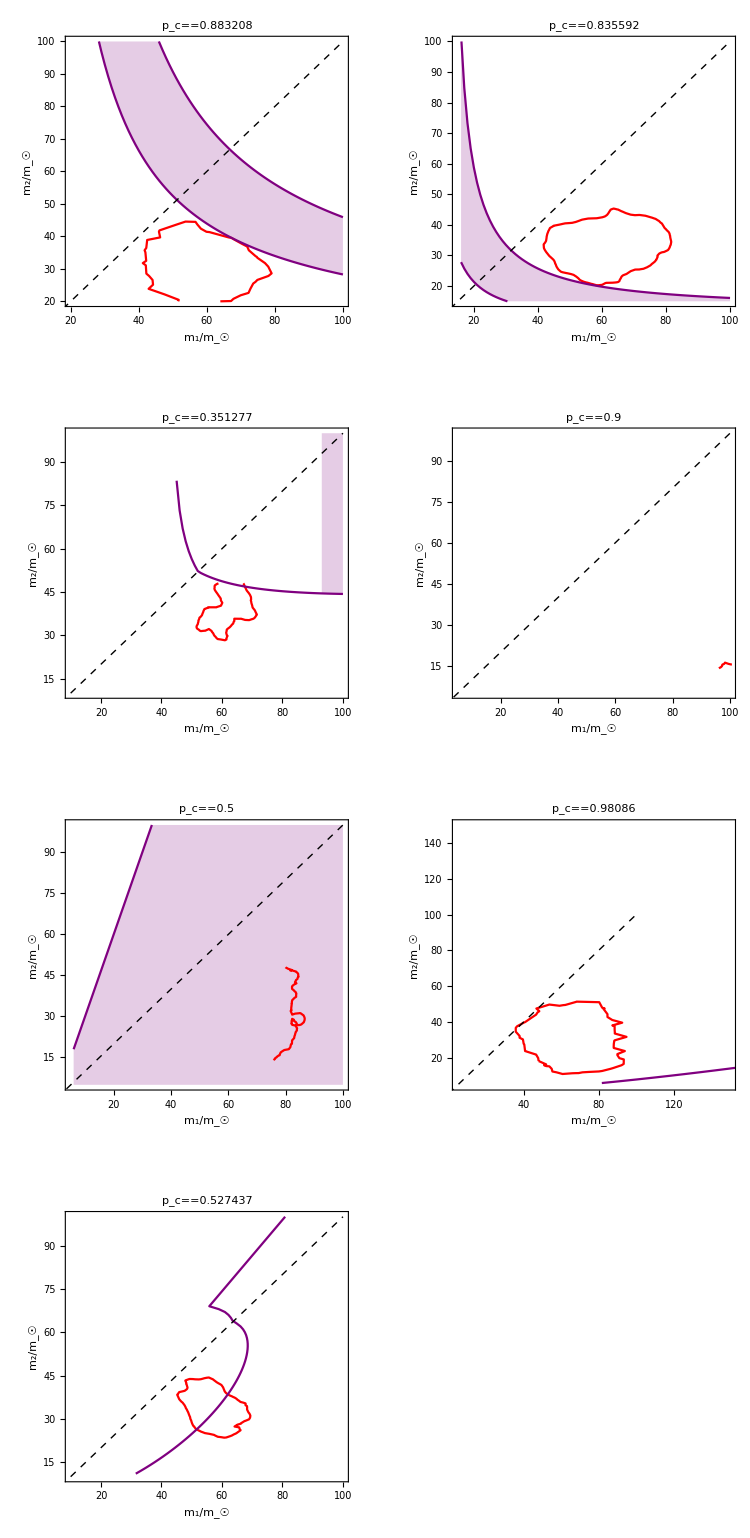

```mathematica
combinedPlot=GraphicsGrid[
Append[Partition[Values[plots],2],{plots[[7]],}],(*将1维数组拆分为3×3的二维网格*)
(*Frame->All,*)(*给每个子图加边框，清晰分隔*)
(*Spacings->{15,15},*)(*控制子图间的水平/垂直间距（像素）*)
ImageSize->750,(*控制整个大图的总尺寸*)
PlotLabel->Style["3×3组合大图",16,Bold]  (*给整个大图加总标题*)]
```

## (old) m1-m2 Plot, 22

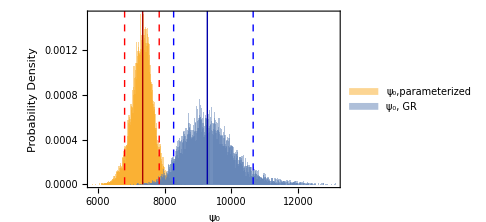

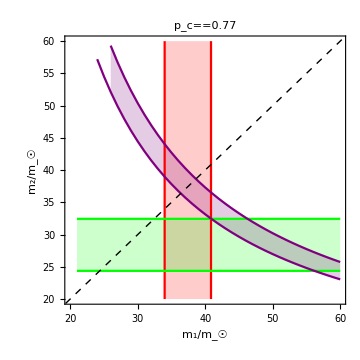

```mathematica
m1s=Range[20,60,1];
m2s=Range[20,60,1];

order=0;
n="cpsi"<>ToString[order];
compPlots[n]=PlotComparisonBetween[samples[n][n],samples[n]["psi"<>ToString[order]],Range[10,100,1],order,BCI[n]["spin1z"][[1]],BCI[n]["spin2z"][[1]]]

prob=0.77;

tapes[n]=<||>;
pInterval[n]=<||>;
pInterval[n]=IntervalFromProbability[prob];

tapeIntervals["mass1"]=Quantile[samples[n]["mass1"],pInterval[n]];
tapeIntervals["mass2"]=Quantile[samples[n]["mass2"],pInterval[n]];

Quiet[
tapeIntervals[n]=Quantile[samples[n][n],pInterval[n]];
tapes[n][n]=HypersurfacePancake[
Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals[n],{m2s},{2},
{order,BCI[n]["spin1z"][[2]],BCI[n]["spin2z"][[2]]},
tapeIntervals["mass2"],2
];
];

tapes[n]["mass1"]={{tapeIntervals["mass1"][[1]],#}&/@m2s,{tapeIntervals["mass1"][[2]],#}&/@m2s};
tapes[n]["mass2"]={{#,tapeIntervals["mass2"][[1]]}&/@m1s,{#,tapeIntervals["mass2"][[2]]}&/@m1s};

lines[n]={
Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[1]][[2;;]],{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],110},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[2]][[2;;]],{{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
tapes[n]["mass2"][[1]][[2;;]],
tapes[n]["mass2"][[2]][[2;;]],

Select[tapes[n][n][[1]][[2;;]],Function[point,m2s[[1]]<=point[[2]]<=m2s[[-1]]]],
Select[tapes[n][n][[2]][[2;;]],Function[point,m2s[[1]]<=point[[2]]<=m2s[[-1]]]]
};
legends[n]=Panel[
Column[{
LineLegend[{Red,Green,Purple,Directive[Black,Dashed]},{
TraditionalForm[Row[{Subscript[m,1]}]],
TraditionalForm[Row[{Subscript[m,2]}]],
TraditionalForm[Row[{Subscript[ψ,0]}]],
TraditionalForm[Subscript[m,1]==Subscript[m,2]]},
LegendLayout->"Column"]},
Spacings->0.2,
Alignment->Left,
Frame->True,
FrameStyle->Directive[Black]
],
Background->White,
FrameMargins->0,
BaseStyle->{FontSize->13}
];

plots[n]=ListLinePlot[
lines[n],
PlotStyle->{Red,Red,Green,Green,Purple,Purple},
Filling->{1->{2},3->{4},5->{6}},
(*FillingStyle->{HatchFilling["Diagonal"]},*)
Axes->False,
Frame->True,
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
FrameLabel->{Row[{Subscript[m,1],"/",Subscript[m,"☉"]}],Row[{Subscript[m,2],"/",Subscript[m,"☉"]}]},
FrameStyle->Directive[Black,Thickness[0.004]],
BaseStyle->{FontSize->15},
AspectRatio->1,
PlotRange->{{m1s[[1]],m1s[[-1]]},{m2s[[1]],m2s[[-1]]}},
Epilog->{
(*White,Opacity[1],Polygon[{{m1s[[-1]],m2s[[-1]]},{m1s[[1]],m2s[[-1]]},{m1s[[1]],m2s[[1]]}}],*)
Inset[
legends[n],Scaled[{0.2,0.82}],{0,0}],
Black,Dashed,Line[{{0,0},{100,100}}]
},
PlotLabel->With[{value=prob},TraditionalForm[HoldForm[Subscript[p,"c"]==value]]],
ImageSize->Medium]
```

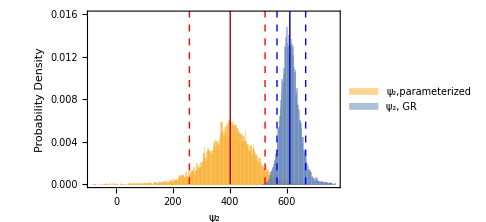

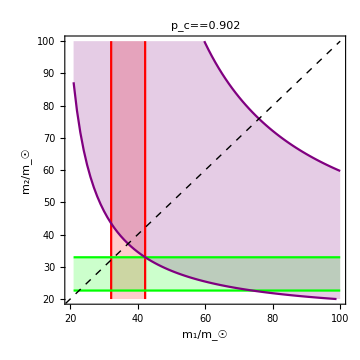

```mathematica
m1s=Range[20,100,1];
m2s=Range[20,100,1];

order=2;
n="cpsi"<>ToString[order];
compPlots[n]=PlotComparisonBetween[samples[n][n],samples[n]["psi"<>ToString[order]],Range[10,100,1],order,BCI[n]["spin1z"][[1]],BCI[n]["spin2z"][[1]]]

prob=0.902;

tapes[n]=<||>;
pInterval[n]=<||>;
pInterval[n]=IntervalFromProbability[prob];

tapeIntervals["mass1"]=Quantile[samples[n]["mass1"],pInterval[n]];
tapeIntervals["mass2"]=Quantile[samples[n]["mass2"],pInterval[n]];

Quiet[
tapeIntervals[n]=Quantile[samples[n][n],pInterval[n]];
tapes[n][n]=HypersurfacePancake[
Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals[n],{m2s},{2},
{2,BCI[n]["spin1z"][[2]],BCI[n]["spin2z"][[2]]},
tapeIntervals["mass2"],2
];
];

tapes[n]["mass1"]={{tapeIntervals["mass1"][[1]],#}&/@m2s,{tapeIntervals["mass1"][[2]],#}&/@m2s};
tapes[n]["mass2"]={{#,tapeIntervals["mass2"][[1]]}&/@m1s,{#,tapeIntervals["mass2"][[2]]}&/@m1s};

lines[n]={Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[1]][[2;;]],{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],110},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[2]][[2;;]],{{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
tapes[n]["mass2"][[1]][[2;;]],
tapes[n]["mass2"][[2]][[2;;]],

tapes[n][n][[1]][[2;;]],
tapes[n][n][[2]][[2;;]]
(*Select[tapes[n][n][[2]][[2;;]],Function[point,m2s[[1]]<=point[[2]]<=m2s[[-1]]]]*)};
legends[n]=Panel[Column[{
LineLegend[{Red,Green,Purple,Directive[Black,Dashed]},{
TraditionalForm[Row[{Subscript[m,1]}]],
TraditionalForm[Row[{Subscript[m,2]}]],
TraditionalForm[Row[{Subscript[ψ,2]}]],
TraditionalForm[Subscript[m,1]==Subscript[m,2]]},
LegendLayout->"Column"]},
Spacings->0.2,
Alignment->Left,
Frame->True,
FrameStyle->Directive[Black]
],
Background->White,
FrameMargins->0
];

plots[n]=ListLinePlot[
lines[n],
PlotStyle->{Red,Red,Green,Green,Purple,Purple},
Axes->True,
Frame->True,
FrameTicks->True,
Filling->{1->{2},3->{4},5->{6}},
FrameLabel->{Row[{Subscript[m,1],"/",Subscript[m,"☉"]}],Row[{Subscript[m,2],"/",Subscript[m,"☉"]}]},
FrameStyle->Directive[Black,Thickness[0.004]],
BaseStyle->{FontSize->15},
AspectRatio->1,
PlotRange->{{m1s[[1]],m1s[[-1]]},{m2s[[1]],m2s[[-1]]}},
Epilog->{
(*White,Opacity[1],Polygon[{{m1s[[-1]],m2s[[-1]]},{m1s[[1]],m2s[[-1]]},{m1s[[1]],m2s[[1]]}}],*)
(*最后绘制图例-优先级最高*)Inset[
legends[n],Scaled[{0.3,0.8}],{0,0}],
Black,Dashed,Line[{{0,0},{100,100}}]
},
PlotLabel->With[{value=prob},TraditionalForm[HoldForm[Subscript[p,"c"]==value]]],
ImageSize->Medium]
```

```mathematica
1-0.902^3
```

0.266129

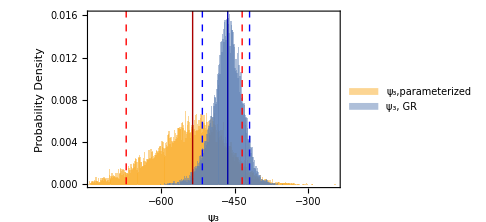

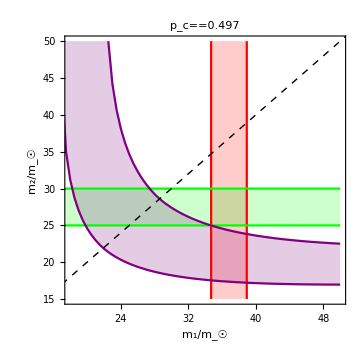

```mathematica
m1s=Range[15,50,1/2];
m2s=Range[15,50,1/2];

order=3;
n="cpsi"<>ToString[order];
compPlots[n]=PlotComparisonBetween[samples[n][n],samples[n]["psi"<>ToString[order]],Range[10,100,1],order,BCI[n]["spin1z"][[1]],BCI[n]["spin2z"][[1]]]


prob=0.497;

tapes[n]=<||>;
pInterval[n]=<||>;
pInterval[n]=IntervalFromProbability[prob];

tapeIntervals["mass1"]=Quantile[samples[n]["mass1"],pInterval[n]];
tapeIntervals["mass2"]=Quantile[samples[n]["mass2"],pInterval[n]];

Quiet[
tapeIntervals[n]=Quantile[samples[n][n],pInterval[n]];
tapes[n][n]=HypersurfacePancake[
Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals[n],{m2s},{2},
{3,BCI[n]["spin1z"][[2]],BCI[n]["spin2z"][[2]]},
tapeIntervals["mass2"],2
];
];

tapes[n]["mass1"]={{tapeIntervals["mass1"][[1]],#}&/@m2s,{tapeIntervals["mass1"][[2]],#}&/@m2s};
tapes[n]["mass2"]={{#,tapeIntervals["mass2"][[1]]}&/@m1s,{#,tapeIntervals["mass2"][[2]]}&/@m1s};

lines[n]={Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[1]][[2;;]],{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],110},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[2]][[2;;]],{{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
tapes[n]["mass2"][[1]][[2;;]],
tapes[n]["mass2"][[2]][[2;;]],

tapes[n][n][[1]][[2;;]],
tapes[n][n][[2]][[2;;]]};
legends[n]=Panel[Column[{
LineLegend[{Red,Green,Purple,Directive[Black,Dashed]},{
TraditionalForm[Row[{Subscript[m,1]}]],
TraditionalForm[Row[{Subscript[m,2]}]],
TraditionalForm[Row[{Subscript[ψ,3]}]],
TraditionalForm[Subscript[m,1]==Subscript[m,2]]},
LegendLayout->"Column"]},
Spacings->0.2,
Alignment->Left,
Frame->True,
FrameStyle->Directive[Black]
],
Background->White,
FrameMargins->0
];

plots[n]=ListLinePlot[
lines[n],
PlotStyle->{Red,Red,Green,Green,Purple,Purple},
Axes->True,
Frame->True,
FrameTicks->True,
Filling->{1->{2},3->{4},5->{6}},
FrameLabel->{Row[{Subscript[m,1],"/",Subscript[m,"☉"]}],Row[{Subscript[m,2],"/",Subscript[m,"☉"]}]},
FrameStyle->Directive[Black,Thickness[0.004]],
BaseStyle->{FontSize->15},
AspectRatio->1,PlotRange->{{18,m1s[[-1]]},{m2s[[1]],m2s[[-1]]}},
Epilog->{
(*White,Opacity[1],Polygon[{{m1s[[-1]],m2s[[-1]]},{m1s[[1]],m2s[[-1]]},{m1s[[1]],m2s[[1]]}}],*)
(*最后绘制图例-优先级最高*)Inset[
legends[n],
Scaled[{0.3,0.8}],{0,0}],
Black,Dashed,Line[{{0,0},{100,100}}]
},
PlotLabel->With[{value=prob},TraditionalForm[HoldForm[Subscript[p,"c"]==value]]],
ImageSize->Medium]
```

```mathematica
1-0.495^3
```

0.878713

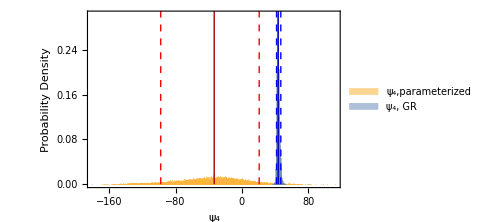

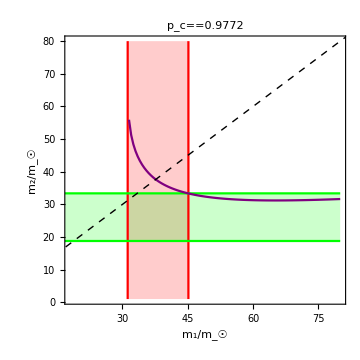

```mathematica
m1s=Range[1,80,1/2];
m2s=Range[1,80,1/2];

order=4;
n="cpsi"<>ToString[order];
compPlots[n]=PlotComparisonBetween[samples[n][n],samples[n]["psi"<>ToString[order]],Range[10,100,1],order,BCI[n]["spin1z"][[1]],BCI[n]["spin2z"][[1]]]


prob=0.9772;

tapes[n]=<||>;
pInterval[n]=<||>;
pInterval[n]=IntervalFromProbability[prob];

tapeIntervals["mass1"]=Quantile[samples[n]["mass1"],pInterval[n]];
tapeIntervals["mass2"]=Quantile[samples[n]["mass2"],pInterval[n]];

Quiet[
tapeIntervals[n]=Quantile[samples[n][n],pInterval[n]];
tapes[n][n]=HypersurfacePancake[
Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals[n],{m2s},{2},
{4,BCI[n]["spin1z"][[2]],BCI[n]["spin2z"][[2]]},
tapeIntervals["mass2"],2
];
];

tapes[n]["mass1"]={{tapeIntervals["mass1"][[1]],#}&/@m2s,{tapeIntervals["mass1"][[2]],#}&/@m2s};
tapes[n]["mass2"]={{#,tapeIntervals["mass2"][[1]]}&/@m1s,{#,tapeIntervals["mass2"][[2]]}&/@m1s};

lines[n]={Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[1]][[2;;]],{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],110},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[2]][[2;;]],{{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
tapes[n]["mass2"][[1]][[2;;]],
tapes[n]["mass2"][[2]][[2;;]],

tapes[n][n][[1]][[2;;]],
tapes[n][n][[2]][[2;;]]
};
legends[n]=Panel[Column[{
LineLegend[{Red,Green,Purple,Directive[Black,Dashed]},{
TraditionalForm[Row[{Subscript[m,1]}]],
TraditionalForm[Row[{Subscript[m,2]}]],
TraditionalForm[Row[{Subscript[ψ,order]}]],
TraditionalForm[Subscript[m,1]==Subscript[m,2]]},
LegendLayout->"Column"]},
Spacings->0.2,
Alignment->Left,
Frame->True,
FrameStyle->Directive[Black]
],
Background->White,
FrameMargins->0
];

plots[n]=ListLinePlot[
lines[n],
PlotStyle->{Red,Red,Green,Green,Purple,Purple},
Axes->True,
Frame->True,
FrameTicks->True,
Filling->{1->{2},3->{4},5->{6}},
FrameLabel->{Row[{Subscript[m,1],"/",Subscript[m,"☉"]}],Row[{Subscript[m,2],"/",Subscript[m,"☉"]}]},
FrameStyle->Directive[Black,Thickness[0.004]],
BaseStyle->{FontSize->15},
AspectRatio->1,PlotRange->{{18,m1s[[-1]]},{m2s[[1]],m2s[[-1]]}},
Epilog->{
(*White,Opacity[1],Polygon[{{m1s[[-1]],m2s[[-1]]},{m1s[[1]],m2s[[-1]]},{m1s[[1]],m2s[[1]]}}],*)
(*最后绘制图例-优先级最高*)Inset[
legends[n],
Scaled[{0.3,0.8}],{0,0}],
Black,Dashed,Line[{{0,0},{100,100}}]
},
PlotLabel->With[{value=prob},TraditionalForm[HoldForm[Subscript[p,"c"]==value]]],
ImageSize->Medium]
```

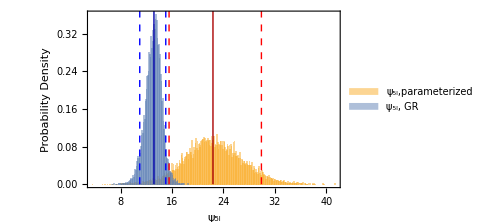

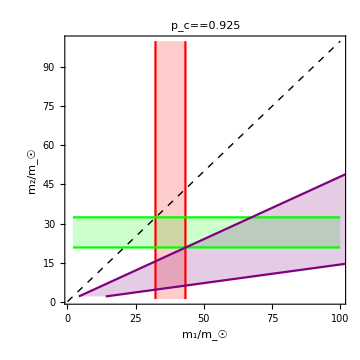

```mathematica
m1s=Range[1,100,1];
m2s=Range[1,100,1];

order="5l";
n="cpsi"<>ToString[order];
compPlots[n]=PlotComparisonBetween[samples[n][n],samples[n]["psi"<>ToString[order]],Range[10,100,1],order,BCI[n]["spin1z"][[1]],BCI[n]["spin2z"][[1]]]


prob=0.9250;

tapes[n]=<||>;
pInterval[n]=<||>;
pInterval[n]=IntervalFromProbability[prob];

tapeIntervals["mass1"]=Quantile[samples[n]["mass1"],pInterval[n]];
tapeIntervals["mass2"]=Quantile[samples[n]["mass2"],pInterval[n]];

Quiet[
tapeIntervals[n]=Quantile[samples[n][n],pInterval[n]];
tapes[n][n]=HypersurfacePancake[
Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals[n],{m2s},{2},
{order,BCI[n]["spin1z"][[2]],BCI[n]["spin2z"][[2]]},
tapeIntervals["mass2"],2
];
];

tapes[n]["mass1"]={{tapeIntervals["mass1"][[1]],#}&/@m2s,{tapeIntervals["mass1"][[2]],#}&/@m2s};
tapes[n]["mass2"]={{#,tapeIntervals["mass2"][[1]]}&/@m1s,{#,tapeIntervals["mass2"][[2]]}&/@m1s};

lines[n]={Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[1]][[2;;]],{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],110},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[2]][[2;;]],{{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
tapes[n]["mass2"][[1]][[2;;]],
tapes[n]["mass2"][[2]][[2;;]],

Reverse/@tapes[n][n][[1]][[2;;]],
Reverse/@tapes[n][n][[2]][[2;;]],
{(Reverse/@tapes[n][n][[1]][[2;;]])[[1]],(Reverse/@tapes[n][n][[2]][[2;;]])[[1]]}(* 补上紫线左边的阴影区 *)
};
legends[n]=Panel[Column[{
LineLegend[{Red,Green,Purple,Directive[Black,Dashed]},{
TraditionalForm[Row[{Subscript[m,1]}]],
TraditionalForm[Row[{Subscript[m,2]}]],
TraditionalForm[Row[{Subscript[ψ,"5l"]}]],
TraditionalForm[Subscript[m,1]==Subscript[m,2]]},
LegendLayout->"Column"]},
Spacings->0.2,
Alignment->Left,
Frame->True,
FrameStyle->Directive[Black]
],
Background->White,
FrameMargins->0
];

plots[n]=ListLinePlot[
lines[n],

PlotStyle->{Red,Red,Green,Green,Purple,Purple,Transparent},
Axes->True,
Frame->True,
FrameTicks->True,
Filling->{1->{2},3->{4},5->{6},5->{7}},
FrameLabel->{Row[{Subscript[m,1],"/",Subscript[m,"☉"]}],Row[{Subscript[m,2],"/",Subscript[m,"☉"]}]},
FrameStyle->Directive[Black,Thickness[0.004]],
BaseStyle->{FontSize->15},
AspectRatio->1,PlotRange->{{m1s[[1]],m1s[[-1]]},{m2s[[1]],m2s[[-1]]}},
Epilog->{
(*White,Opacity[1],Polygon[{{m1s[[-1]],m2s[[-1]]},{m1s[[1]],m2s[[-1]]},{m1s[[1]],m2s[[1]]}}],*)
(*最后绘制图例-优先级最高*)Inset[
legends[n],Scaled[{0.3,0.8}],{0,0}],
Black,Dashed,Line[{{0,0},{100,100}}]},
FrameLabel->{Row[{Subscript[m,1],"/",Subscript[m,"☉"]}],Row[{Subscript[m,2],"/",Subscript[m,"☉"]}]},
PlotLabel->With[{value=prob},TraditionalForm[HoldForm[Subscript[p,"c"]==value]]],
ImageSize->Medium]
```

```mathematica
BCI[n][n]
```

{15.535,22.3649,29.9001}

```mathematica
1-0.925^3
```

0.208547

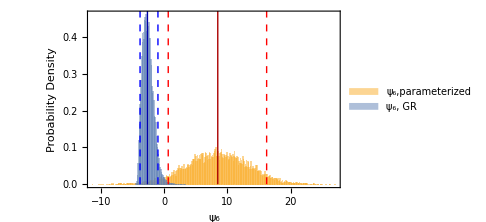

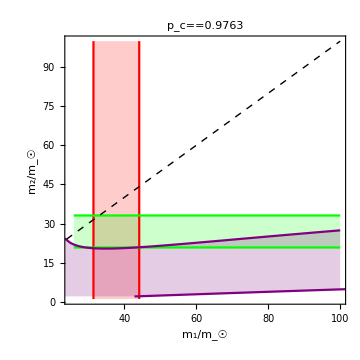

```mathematica
m1s=Range[25,100,1];
m2s=Range[1,100,1];

order=6;
n="cpsi"<>ToString[order];
compPlots[n]=PlotComparisonBetween[samples[n][n],samples[n]["psi"<>ToString[order]],Range[10,100,1],order,BCI[n]["spin1z"][[1]],BCI[n]["spin2z"][[1]]]

prob=0.9763;

tapes[n]=<||>;
pInterval[n]=<||>;
pInterval[n]=IntervalFromProbability[prob];

tapeIntervals["mass1"]=Quantile[samples[n]["mass1"],pInterval[n]];
tapeIntervals["mass2"]=Quantile[samples[n]["mass2"],pInterval[n]];

Quiet[
tapeIntervals[n]=Quantile[samples[n][n],pInterval[n]];
tapes[n][n]=HypersurfacePancake[
Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals[n],{m2s},{2},
{order,BCI[n]["spin1z"][[2]],BCI[n]["spin2z"][[2]]},
tapeIntervals["mass2"],2
];
];

tapes[n]["mass1"]={{tapeIntervals["mass1"][[1]],#}&/@m2s,{tapeIntervals["mass1"][[2]],#}&/@m2s};
tapes[n]["mass2"]={{#,tapeIntervals["mass2"][[1]]}&/@m1s,{#,tapeIntervals["mass2"][[2]]}&/@m1s};

lines[n]={Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[1]][[2;;]],{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],110},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[2]][[2;;]],{{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
tapes[n]["mass2"][[1]][[2;;]],
tapes[n]["mass2"][[2]][[2;;]],

tapes[n][n][[1]][[2;;]],
Reverse/@tapes[n][n][[2]][[2;;]],
{(Reverse/@tapes[n][n][[1]][[2;;]])[[1]],(Reverse/@tapes[n][n][[2]][[2;;]])[[1]]}(* 补上紫线左边的阴影区 *)
};
legends[n]=Panel[Column[{
LineLegend[{Red,Green,Purple,Directive[Black,Dashed]},{
TraditionalForm[Row[{Subscript[m,1]}]],
TraditionalForm[Row[{Subscript[m,2]}]],
TraditionalForm[Row[{Subscript[ψ,order]}]],
TraditionalForm[Subscript[m,1]==Subscript[m,2]]},
LegendLayout->"Column"]},
Spacings->0.2,
Alignment->Left,
Frame->True,
FrameStyle->Directive[Black]
],
Background->White,
FrameMargins->0
];

plots[n]=ListLinePlot[
lines[n],

PlotStyle->{Red,Red,Green,Green,Purple,Purple,Transparent},
Axes->True,
Frame->True,
FrameTicks->True,
Filling->{1->{2},3->{4},5->{6},5->{7}},
FrameLabel->{Row[{Subscript[m,1],"/",Subscript[m,"☉"]}],Row[{Subscript[m,2],"/",Subscript[m,"☉"]}]},
FrameStyle->Directive[Black,Thickness[0.004]],
BaseStyle->{FontSize->15},
AspectRatio->1,PlotRange->{{m1s[[1]],m1s[[-1]]},{m2s[[1]],m2s[[-1]]}},
Epilog->{
(*White,Opacity[1],Polygon[{{m1s[[-1]],m2s[[-1]]},{m1s[[1]],m2s[[-1]]},{m1s[[1]],m2s[[1]]}}],*)
(*最后绘制图例-优先级最高*)Inset[
legends[n],Scaled[{0.3,0.8}],{0,0}],
Black,Dashed,Line[{{0,0},{100,100}}]},
FrameLabel->{Row[{Subscript[m,1],"/",Subscript[m,"☉"]}],Row[{Subscript[m,2],"/",Subscript[m,"☉"]}]},
PlotLabel->With[{value=prob},TraditionalForm[HoldForm[Subscript[p,"c"]==value]]],
ImageSize->Medium]
```

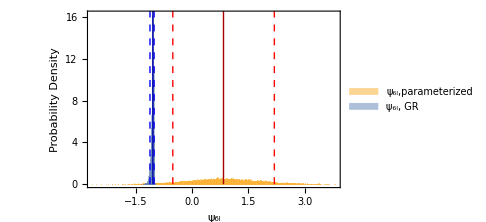

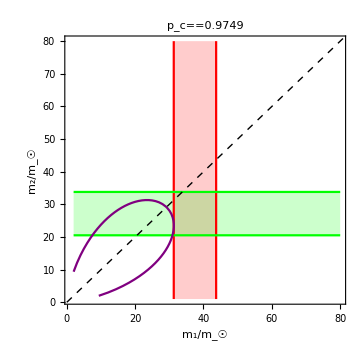

```mathematica
m1s=Range[1,80,1];
m2s=Range[1,80,1];

order="6l";
n="cpsi"<>ToString[order];
compPlots[n]=PlotComparisonBetween[samples[n][n],samples[n]["psi"<>ToString[order]],Range[10,100,1],order,BCI[n]["spin1z"][[1]],BCI[n]["spin2z"][[1]]]


prob=0.9749;
(*prob=0.9891;*)

tapes[n]=<||>;
pInterval[n]=<||>;
pInterval[n]=IntervalFromProbability[prob];

tapeIntervals["mass1"]=Quantile[samples[n]["mass1"],pInterval[n]];
tapeIntervals["mass2"]=Quantile[samples[n]["mass2"],pInterval[n]];

Quiet[
tapeIntervals[n]=Quantile[samples[n][n],pInterval[n]];
tapes[n][n]=HypersurfacePancake[
Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals[n],{m2s},{2},
{order,BCI[n]["spin1z"][[2]],BCI[n]["spin2z"][[2]]},
tapeIntervals["mass2"],2
];
];

tapes[n]["mass1"]={{tapeIntervals["mass1"][[1]],#}&/@m2s,{tapeIntervals["mass1"][[2]],#}&/@m2s};
tapes[n]["mass2"]={{#,tapeIntervals["mass2"][[1]]}&/@m1s,{#,tapeIntervals["mass2"][[2]]}&/@m1s};

lines[n]={Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[1]][[2;;]],{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],110},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
Join[{{tapes[n]["mass1"][[1]][[2;;]][[1]][[1]],-10},{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],-10}},tapes[n]["mass1"][[2]][[2;;]],{{tapes[n]["mass1"][[2]][[2;;]][[1]][[1]],110}}],
tapes[n]["mass2"][[1]][[2;;]],
tapes[n]["mass2"][[2]][[2;;]],

Join[Reverse/@Select[Reverse/@tapes[n][n][[1]][[2;;]],#[[1]]>=#[[2]]&],Reverse[Select[Reverse/@tapes[n][n][[1]][[2;;]],#[[1]]>=#[[2]]&]]],
Reverse/@tapes[n][n][[2]][[2;;]],
{(Reverse/@tapes[n][n][[1]][[2;;]])[[1]],(Reverse/@tapes[n][n][[2]][[2;;]])[[1]]}(* 补上紫线左边的阴影区 *)
};
legends[n]=Panel[Column[{
LineLegend[{Red,Green,Purple,Directive[Black,Dashed]},{
TraditionalForm[Row[{Subscript[m,1]}]],
TraditionalForm[Row[{Subscript[m,2]}]],
TraditionalForm[Row[{Subscript[ψ,order]}]],
TraditionalForm[Subscript[m,1]==Subscript[m,2]]},
LegendLayout->"Column"]},
Spacings->0.2,
Alignment->Left,
Frame->True,
FrameStyle->Directive[Black]
],
Background->White,
FrameMargins->0
];

plots[n]=ListLinePlot[
lines[n],

PlotStyle->{Red,Red,Green,Green,Purple,Purple,Transparent},
Axes->True,
Frame->True,
FrameTicks->True,
Filling->{1->{2},3->{4},5->{6},5->{7}},
FrameLabel->{Row[{Subscript[m,1],"/",Subscript[m,"☉"]}],Row[{Subscript[m,2],"/",Subscript[m,"☉"]}]},
FrameStyle->Directive[Black,Thickness[0.004]],
BaseStyle->{FontSize->15},
AspectRatio->1,PlotRange->{{m1s[[1]],m1s[[-1]]},{m2s[[1]],m2s[[-1]]}},
Epilog->{
(*White,Opacity[1],Polygon[{{m1s[[-1]],m2s[[-1]]},{m1s[[1]],m2s[[-1]]},{m1s[[1]],m2s[[1]]}}],*)
(*最后绘制图例-优先级最高*)Inset[
legends[n],Scaled[{0.3,0.8}],{0,0}],
Black,Dashed,Line[{{0,0},{100,100}}]},
FrameLabel->{Row[{Subscript[m,1],"/",Subscript[m,"☉"]}],Row[{Subscript[m,2],"/",Subscript[m,"☉"]}]},
PlotLabel->With[{value=prob},TraditionalForm[HoldForm[Subscript[p,"c"]==value]]],
ImageSize->Medium]
```

Part::partw: Part 7 of … does not exist.

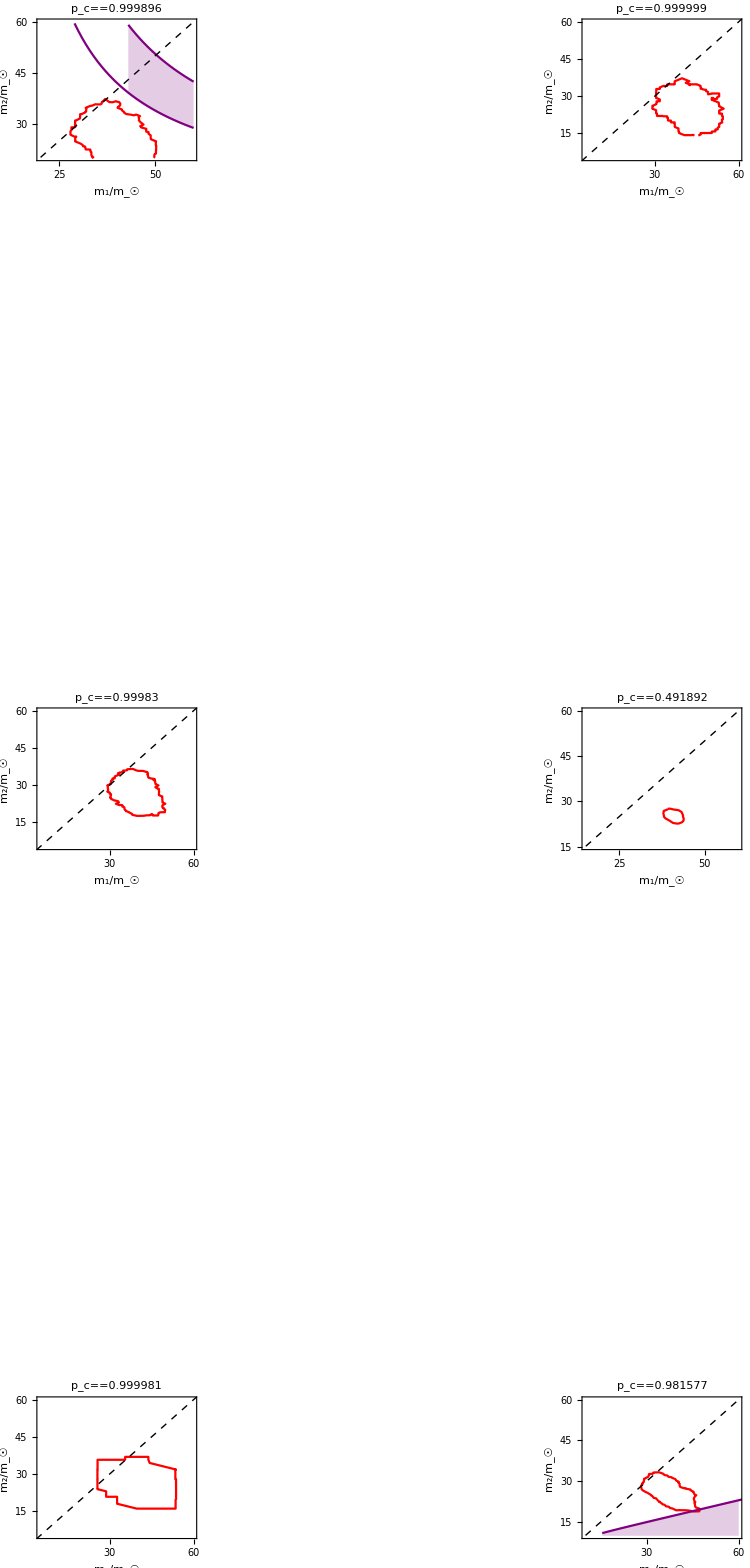

```mathematica
combinedPlot=GraphicsGrid[
Append[Partition[Values[plots],2],{plots[[7]],}],(*将1维数组拆分为3×3的二维网格*)
(*Frame->All,*)(*给每个子图加边框，清晰分隔*)
(*Spacings->{15,15},*)(*控制子图间的水平/垂直间距（像素）*)
ImageSize->750,(*控制整个大图的总尺寸*)
PlotLabel->Style["3×3组合大图",16,Bold]  (*给整个大图加总标题*)]
```

## Value Domains

```mathematica
vd=<||>;
```

```mathematica
(BCI["cpsi0"]["cpsi0"][[3]]-BCI["cpsi0"]["cpsi0"][[1]])/5000
vd["cpsi0"]=Manipulate[
Plot3D[
Function[{m1,m2},Psi[0,η[m1,m2],M[m1,m2],spin1z,spin2z]][m1,m2],
{m1,BCI["cpsi0"]["mass1"][[1]],BCI["cpsi0"]["mass1"][[3]]},
{m2,BCI["cpsi0"]["mass2"][[1]],BCI["cpsi0"]["mass2"][[3]]},
PlotPoints->{20,20},
RegionFunction->Function[{m1,m2,psi},m1>m2],
ColorFunction->(If[#3<=-800,Red,Blue]&),
ColorFunctionScaling->False,
AxesLabel->{TraditionalForm[Subscript[m,1]/Subscript[m,"☉"]],TraditionalForm[Subscript[m,2]/Subscript[m,"☉"]],TraditionalForm[Subscript[ψ,0]]}
],
{spin1z,BCI["cpsi0"]["spin1z"][[2]]},{spin2z,BCI["cpsi0"]["spin2z"][[2]]}
]
```

0.206569

```mathematica
(BCI["cpsi2"]["cpsi2"][[3]]-BCI["cpsi2"]["cpsi2"][[1]])/250
vd["cpsi0"]=Manipulate[
Plot3D[
Function[{m1,m2},Psi[2,η[m1,m2],M[m1,m2],spin1z,spin2z]][m1,m2],
{m1,BCI["cpsi2"]["mass1"][[1]],BCI["cpsi2"]["mass1"][[3]]},
{m2,BCI["cpsi2"]["mass2"][[1]],BCI["cpsi2"]["mass2"][[3]]},
PlotPoints->{20,20},
RegionFunction->Function[{m1,m2,psi},m1>m2],
ColorFunction->(If[#3<=-800,Red,Blue]&),
ColorFunctionScaling->False
],
{spin1z,BCI["cpsi2"]["spin1z"][[2]]},{spin2z,BCI["cpsi2"]["spin2z"][[2]]}
]
```

1.06474

```mathematica
(BCI["cpsi3"]["cpsi3"][[3]]-BCI["cpsi3"]["cpsi3"][[1]])/150
Manipulate[
Plot3D[
Function[{m1,m2},Psi[3,η[m1,m2],M[m1,m2],spin1z,spin2z]][m1,m2],
{m1,BCI["cpsi3"]["mass1"][[1]],BCI["cpsi3"]["mass1"][[3]]},
{m2,BCI["cpsi3"]["mass2"][[1]],BCI["cpsi3"]["mass2"][[3]]},
PlotPoints->{20,20},
RegionFunction->Function[{m1,m2,psi},m1>m2],
ColorFunction->(If[#3<=-800,Red,Blue]&),
ColorFunctionScaling->False
],
{spin1z,BCI["cpsi3"]["spin1z"][[2]]},{spin2z,BCI["cpsi3"]["spin2z"][[2]]}
]
```

1.57419

Part::partw: Part 3 of Missing[KeyAbsent,cpsi3][mass1] does not exist.

Plot3D::plln: Limiting value mass1 in {m1,mass1,Missing[KeyAbsent,cpsi3][mass1]⟦3⟧} is not a machine-sized real number.

```mathematica
(BCI["cpsi4"]["cpsi4"][[3]]-BCI["cpsi4"]["cpsi4"][[1]])/5
Manipulate[
Plot3D[
Function[{m1,m2},Psi[4,η[m1,m2],M[m1,m2],spin1z,spin2z]][m1,m2],
{m1,BCI["cpsi4"]["mass1"][[1]],BCI["cpsi4"]["mass1"][[3]]},
{m2,BCI["cpsi4"]["mass2"][[1]],BCI["cpsi4"]["mass2"][[3]]},
PlotPoints->{20,20},
RegionFunction->Function[{m1,m2,psi},m1>m2],
ColorFunction->(If[#3<=-800,Red,Blue]&),
ColorFunctionScaling->False
],
{spin1z,BCI["cpsi4"]["spin1z"][[2]]},{spin2z,BCI["cpsi4"]["spin2z"][[2]]}
]
```

23.7613

```mathematica
(BCI["cpsi5l"]["cpsi5l"][[3]]-BCI["cpsi5l"]["cpsi5l"][[1]])/1.5
Manipulate[
Plot3D[
Function[{m1,m2},Psi["5l",η[m1,m2],M[m1,m2],spin1z,spin2z]][m1,m2],
{m1,BCI["cpsi5l"]["mass1"][[1]],BCI["cpsi5l"]["mass1"][[3]]},
{m2,BCI["cpsi5l"]["mass2"][[1]],BCI["cpsi5l"]["mass2"][[3]]},
PlotPoints->{20,20},
RegionFunction->Function[{m1,m2,psi},m1>m2],
ColorFunction->(If[#3<=-800,Red,Blue]&),
ColorFunctionScaling->False
],
{spin1z,BCI["cpsi5l"]["spin1z"][[2]]},{spin2z,BCI["cpsi5l"]["spin2z"][[2]]}
]
```

9.56092

```mathematica
Manipulate[
Plot3D[
Function[{m1,m2},Psi["5l",η[m1,m2],M[m1,m2],spin1z,spin2z]][m1,m2],
{m1,3,100},
{m2,3,100},
PlotPoints->{20,20},
RegionFunction->Function[{m1,m2,psi},m1>m2],
ColorFunction->(If[#3<=-800,Red,Blue]&),
ColorFunctionScaling->False
],
{spin1z,BCI["cpsi5l"]["spin1z"][[2]]},{spin2z,BCI["cpsi5l"]["spin2z"][[2]]}
]
```

```mathematica
(BCI["cpsi6"]["cpsi6"][[3]]-BCI["cpsi6"]["cpsi6"][[1]])/0.5
Manipulate[
Plot3D[
Function[{m1,m2},Psi[6,η[m1,m2],M[m1,m2],spin1z,spin2z]][m1,m2],
{m1,BCI["cpsi6"]["mass1"][[1]],BCI["cpsi6"]["mass1"][[3]]},
{m2,BCI["cpsi6"]["mass2"][[1]],BCI["cpsi6"]["mass2"][[3]]},
PlotPoints->{20,20},
RegionFunction->Function[{m1,m2,psi},m1>m2],
ColorFunction->(If[#3<=-800,Red,Blue]&),
ColorFunctionScaling->False
],
{spin1z,BCI["cpsi6"]["spin1z"][[2]]},{spin2z,BCI["cpsi6"]["spin2z"][[2]]}
]
```

31.1398

```mathematica
(BCI["cpsi6l"]["cpsi6l"][[3]]-BCI["cpsi6l"]["cpsi6l"][[1]])/0.1
Manipulate[
Plot3D[
Function[{m1,m2},Psi["6l",η[m1,m2],M[m1,m2],spin1z,spin2z]][m1,m2],
{m1,BCI["cpsi6l"]["mass1"][[1]],BCI["cpsi6l"]["mass1"][[3]]},
{m2,BCI["cpsi6l"]["mass2"][[1]],BCI["cpsi6l"]["mass2"][[3]]},
PlotPoints->{20,20},
RegionFunction->Function[{m1,m2,psi},m1>m2],
ColorFunction->(If[#3<=-800,Red,Blue]&),
ColorFunctionScaling->False
],
{spin1z,BCI["cpsi6l"]["spin1z"][[2]]},{spin2z,BCI["cpsi6l"]["spin2z"][[2]]}
]
```

27.0383

```mathematica
(*Manipulate[
Plot3D[
Function[{m1,m2},Psi[7,η[m1,m2],M[m1,m2],spin1z,spin2z]][m1,m2],
{m1,20,80},
{m2,20,80},
PlotPoints->{20,20},
RegionFunction->Function[{m1,m2,psi},m1>m2],
ColorFunction->(If[#3<=-800,Red,Blue]&),
ColorFunctionScaling->False
],
{spin1z,0.06070798549182338},{spin2z,0.09392835788044217}
(*{spin1z,-1,1},{spin2z,-1,1}*)
]*)
```

## Exports

```mathematica
Do[
name=deviationNames[[i]];
exportPath=StringJoin["D:/Documents/workspace/课题/论文/figs/GW150914/comp_plots/","GW150914_inverse_plot_",
name,
".pdf"];
Export[exportPath,compPlots[name],"PDF",ImageResolution->1000],
{i,1,Length[deviationNames]}]
```

```mathematica
Do[
name=deviationNames[[i]];
exportPath=StringJoin["D:/Documents/workspace/课题/论文/figs/GW150914/inverse_plots/","GW150914_inverse_plot_",
name,
".pdf"];
Export[exportPath,plots[name],"PDF",ImageResolution->1000],
{i,1,Length[deviationNames]}]
```

```mathematica
Export["D:/Documents/workspace/课题/论文/figs/GW150914/inverse_plots/GW150914_patch_cpsi6.pdf",patch6,"PDF",ImageResolution->1000]
```

D:/Documents/workspace/课题/论文/figs/GW150914/inverse_plots/GW150914_patch_cpsi6.pdf

```mathematica
Do[
name=deviationNames[[i]];
exportPath=StringJoin["D:/Documents/workspace/课题/论文/figs/GW150914/value_domains/","GW150914_vd_",
name,
".pdf"];
Export[exportPath,vd[name],"PDF",ImageResolution->1000],
{i,1,Length[deviationNames]}]
```

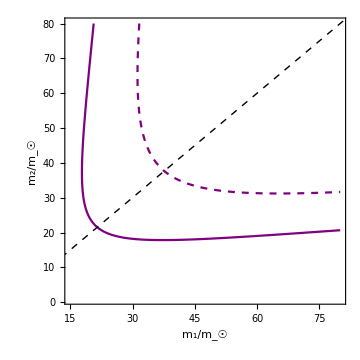

```mathematica
m1s=Range[15,80,1];
m2s=Range[1,80,1];

order=4;
n="cpsi"<>ToString[order];

prob1=0.9772;
(*再大一点会扫过这个矩形*)
prob2=0.989;

tapes[n]=<||>;
pInterval[n]=<||>;
pInterval[n]=IntervalFromProbability[prob];
pInterval[n]=Join[IntervalFromProbability[prob2],IntervalFromProbability[prob1]];

tapeIntervals["mass1"]=Quantile[samples[n]["mass1"],pInterval[n]];
tapeIntervals["mass2"]=Quantile[samples[n]["mass2"],pInterval[n]];

Quiet[
tapeIntervals[n]=Quantile[samples[n][n],pInterval[n]];
tapes[n][n]=HypersurfacePancake[
Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals[n],{m1s},{2},
{4,BCI[n]["spin1z"][[2]],BCI[n]["spin2z"][[2]]},
tapeIntervals["mass2"],2
];
];

tapes[n]["mass1"]={{tapeIntervals["mass1"][[1]],#}&/@m2s,{tapeIntervals["mass1"][[2]],#}&/@m2s};
tapes[n]["mass2"]={{#,tapeIntervals["mass2"][[1]]}&/@m1s,{#,tapeIntervals["mass2"][[2]]}&/@m1s};

lines[n]={
Join[Reverse[Reverse/@Select[tapes[n][n][[2]][[2;;]],#[[1]]>=#[[2]]&]],Select[tapes[n][n][[2]][[2;;]],#[[1]]>=#[[2]]&]],
Join[Reverse[Reverse/@Select[tapes[n][n][[4]][[2;;]],#[[1]]>=#[[2]]&]],Select[tapes[n][n][[4]][[2;;]],#[[1]]>=#[[2]]&]]
(*tapes[n][n][[2]][[2;;]],
tapes[n][n][[4]][[2;;]]*)
};
legends[n]=Panel[
Column[{
LineLegend[{Directive[Purple,Dashed],Purple,Directive[Black,Dashed]},{
TraditionalForm[Row[{Subscript[ψ,4],", ",With[{value=prob1},TraditionalForm[HoldForm[p==value]]]}]],
TraditionalForm[Row[{Subscript[ψ,4],", ",With[{value=prob2},TraditionalForm[HoldForm[p==value]]]}]],
TraditionalForm[Subscript[m,1]==Subscript[m,2]]},
LegendLayout->"Column"]},
Spacings->0.2,
Alignment->Left](*,
Background->White*)
];

plots[n]=ListLinePlot[
lines[n],
PlotStyle->{
Purple,
Directive[Purple,Dashed]
},
Axes->True,
Frame->True,
FrameTicks->True,
Filling->{
(*1->{2},3->{4},*)
(*6->{7},8->{9},*)
5->{10}},
FillingStyle->{HatchFilling["Diagonal"]},
FrameLabel->{Row[{Subscript[m,1],"/",Subscript[m,"☉"]}],Row[{Subscript[m,2],"/",Subscript[m,"☉"]}]},
FrameStyle->Directive[Black,Thickness[0.004]],
BaseStyle->{FontSize->15},
AspectRatio->1,
PlotRange->{{m1s[[1]],m1s[[-1]]},{m2s[[1]],1m2s[[-1]]}},
Epilog->{
(*White,Opacity[1],Polygon[{{m1s[[-1]],m2s[[-1]]},{m1s[[1]],m2s[[-1]]},{m1s[[1]],m2s[[1]]}}],*)
Black,Dashed,Line[{{0,0},{100,100}}],
Inset[
legends[n],
Scaled[{0.3,0.8}],
{0,0}
]
},
(*PlotLabel->With[{value=prob},TraditionalForm[HoldForm[p==value]]],*)
ImageSize->Medium]
```

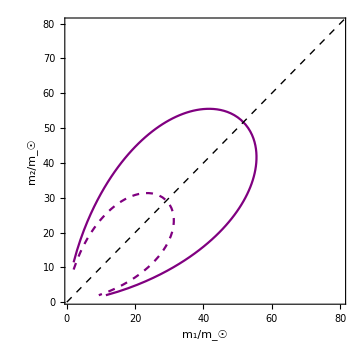

```mathematica
m1s=Range[1,80,1];
m2s=Range[1,80,1];

order="6l";
n="cpsi"<>ToString[order];

prob1=0.9749;
prob2=0.9891;

tapes[n]=<||>;
pInterval[n]=<||>;
pInterval[n]=IntervalFromProbability[prob];
pInterval[n]=Join[IntervalFromProbability[prob2],IntervalFromProbability[prob1]];

tapeIntervals["mass1"]=Quantile[samples[n]["mass1"],pInterval[n]];
tapeIntervals["mass2"]=Quantile[samples[n]["mass2"],pInterval[n]];

Quiet[
tapeIntervals[n]=Quantile[samples[n][n],pInterval[n]];
tapes[n][n]=HypersurfacePancake[
Function[{l,m1,m2,χ1L,χ2L},Psi[l,η[m1,m2],M[m1,m2],χ1L,χ2L]],
tapeIntervals[n],{m1s},{2},
{order,BCI[n]["spin1z"][[2]],BCI[n]["spin2z"][[2]]},
tapeIntervals["mass2"],2
];
];

tapes[n]["mass1"]={{tapeIntervals["mass1"][[1]],#}&/@m2s,{tapeIntervals["mass1"][[2]],#}&/@m2s};
tapes[n]["mass2"]={{#,tapeIntervals["mass2"][[1]]}&/@m1s,{#,tapeIntervals["mass2"][[2]]}&/@m1s};

lines[n]={
(*Join[Reverse[Reverse/@Select[tapes[n][n][[1]][[2;;]],#[[1]]>=#[[2]]&]],Select[tapes[n][n][[1]][[2;;]],#[[1]]>=#[[2]]&]],
Join[Reverse[Reverse/@Select[tapes[n][n][[3]][[2;;]],#[[1]]>=#[[2]]&]],Select[tapes[n][n][[3]][[2;;]],#[[1]]>=#[[2]]&]]*)
Join[Reverse/@Select[Reverse/@tapes[n][n][[1]][[2;;]],#[[1]]>=#[[2]]&],Reverse[Select[Reverse/@tapes[n][n][[1]][[2;;]],#[[1]]>=#[[2]]&]]],
Join[Reverse/@Select[Reverse/@tapes[n][n][[3]][[2;;]],#[[1]]>=#[[2]]&],Reverse[Select[Reverse/@tapes[n][n][[3]][[2;;]],#[[1]]>=#[[2]]&]]]
};
legends[n]=Panel[
Column[{
LineLegend[{Directive[Purple,Dashed],Purple,Directive[Black,Dashed]},{
TraditionalForm[Row[{Subscript[ψ,order],", ",With[{value=prob1},TraditionalForm[HoldForm[p==value]]]}]],
TraditionalForm[Row[{Subscript[ψ,order],", ",With[{value=prob2},TraditionalForm[HoldForm[p==value]]]}]],
TraditionalForm[Subscript[m,1]==Subscript[m,2]]},
LegendLayout->"Column"]},
Spacings->0.2,
Alignment->Left](*,
Background->White*)
];

patch6=ListLinePlot[
{
(*Join[Reverse[Reverse/@Select[tapes[n][n][[1]][[2;;]],#[[1]]>=#[[2]]&]],Select[tapes[n][n][[1]][[2;;]],#[[1]]>=#[[2]]&]],
Join[Reverse[Reverse/@Select[tapes[n][n][[3]][[2;;]],#[[1]]>=#[[2]]&]],Select[tapes[n][n][[3]][[2;;]],#[[1]]>=#[[2]]&]]*)
tapes[n][n][[1]][[2;;]],
tapes[n][n][[3]][[2;;]]
},
PlotStyle->{
Purple,
Directive[Purple,Dashed]
},

Filling->{
(*1->{2},3->{4},*)
(*6->{7},8->{9},*)
5->{10}},
FillingStyle->{HatchFilling["Diagonal"]},
AspectRatio->1,
PlotRange->{{40.02,40.026},{30.015,30.020}},
Epilog->{
(*White,Opacity[1],Polygon[{{m1s[[-1]],m2s[[-1]]},{m1s[[1]],m2s[[-1]]},{m1s[[1]],m2s[[1]]}}],*)
Black,Dashed,Line[{{0,0},{100,100}}]
},
Axes->False,
Frame->True,
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
FrameLabel->{Row[{Subscript[m,1],"/",Subscript[m,"☉"]}],Row[{Subscript[m,2],"/",Subscript[m,"☉"]}]},
FrameStyle->Directive[Black,Thickness[0.004]],
BaseStyle->{FontSize->15},
(*PlotLabel->With[{value=prob},TraditionalForm[HoldForm[p==value]]],*)
ImageSize->Medium];

plots[n]=ListLinePlot[
lines[n],
PlotStyle->{
Purple,
Directive[Purple,Dashed]
},

Axes->True,
Frame->True,
FrameTicks->True,
Filling->{
(*1->{2},3->{4},*)
(*6->{7},8->{9},*)
5->{10}},
FillingStyle->{HatchFilling["Diagonal"]},
FrameLabel->{Row[{Subscript[m,1],"/",Subscript[m,"☉"]}],Row[{Subscript[m,2],"/",Subscript[m,"☉"]}]},
FrameStyle->Directive[Black,Thickness[0.004]],
BaseStyle->{FontSize->15},
AspectRatio->1,
PlotRange->{{m1s[[1]],m1s[[-1]]},{m2s[[1]],1m2s[[-1]]}},
Epilog->{
(*White,Opacity[1],Polygon[{{m1s[[-1]],m2s[[-1]]},{m1s[[1]],m2s[[-1]]},{m1s[[1]],m2s[[1]]}}],*)
Inset[
legends[n],
Scaled[{0.3,0.8}],
{0,0}
],
Black,Dashed,Line[{{0,0},{100,100}}](*,
Inset[
patch6]*)
},
(*PlotLabel->With[{value=prob},TraditionalForm[HoldForm[p==value]]],*)
ImageSize->Medium]
```

```mathematica
name="cpsi6l";
exportPath=StringJoin["D:/Documents/workspace/课题/论文/figs/GW150914/inverse_plots/","GW150914_inverse_plot_",
name,
"_double",
".pdf"];
Export[exportPath,plots[name],"PDF",ImageResolution->1000]
```

D:/Documents/workspace/课题/论文/figs/GW150914/inverse_plots/GW150914_inverse_plot_cpsi6l_double.pdf